# Warp Drives in 5 Dimensions

## Accompanying Calculations and Visualizations

Alicia Marie Savelli

Department of Physics, Brock University
1812 Sir Isaac Brock Way, St. Catharines, Ontario, L2S 3A1, Canada

Canadian Institute for Theoretical Astrophysics, University of Toronto 
60 St. George St., Toronto, Ontario, M5S 3H8, Canada

David A. Dunlap Department of Astronomy and Astrophysics, University of Toronto 
50 St. George St., Toronto, Ontario, M5S 3H4, Canada

Faster-than-light (FTL) travel has long been hypothesized in science-fiction writing as a preferred method of interstellar travel. Although forbidden in Special Relativity, FTL travel may be allowed within the constraints of General Relativity as a result of the introduction of curvature in the spacetime geometry. One of the most popular proposed methods of FTL travel is Alcubierre’s warp drive (Alcubierre, 1994). The problem with the warp drive and other current proposals for FTL travel is that they require huge amounts of exotic matter, or negative energy density, to operate. In this paper, we aim to find a realistic solution for FTL travel by creating a spacetime geometry that will reduce or eliminate entirely these negative energy requirements. Our spacetime geometry is created through a modification to the original warp drive that has never yet been considered: the addition of a fifth spacetime dimension, called hyperspace. We considered both infinite and compactified hyperspace dimensions. It was found that this new dimension is able to “store” additional energy density. In addition to the hyperspace dimension, we also introduced new parameters into the metric that were free to vary in order to minimize further the energy requirement. With certain choices in parameter values, the magnitude of the total energy requirement could be made arbitrarily small. The infinite hyperspace dimension produced the most realistic result of a warp drive with a total energy requirement of -1.00×10^-20 v^2 M_☉ for warp bubble the size of a spaceship or -9.27×10^-46 v^2 M_☉ for a warp bubble the size of a particle. It was also found that our metric could be represented as a Natario spacetime through a simple change of coordinates. Future research should explore more generalized motion for the warp drive, more options for the characteristics of the fifth dimension, and the resulting matter needed to generate the warp drive.

## Introduction

This Mathematica notebook includes all calculations and plots for my Warp Drives in 5 Dimensions paper.  We use the OGRe package (Shoshany, 2021) to compute all General Relativity calculations.

We first include a few initialization cells that should be run prior to any calculations.  These cells define various functions and properties used throughout the notebook.

We then run a check for the energy density expression ρ and the total energy E of the original 4D Alcubierre warp drive.  We have also included various plots of the energy density.

Next are all of our calculations and plots for our 5D warp drive.  We begin by building the metric, determining the geodesic, and calculating the energy density ρ and the total energy E of our warp drive.  We include all calculations and plots for all regularization function options for the fifth dimension.  

Finally, we derive the coordinate transformation that allows us to write our 5D warp drive as a Natario spacetime, and ensure through a simple substitution that our warp drive really is of Natario form.

Please note that the energy density plots in this notebook, particularly the 3D ones, may take a few minutes to run. If you’d like a shorter runtime, set PlotPoints to a smaller number (this can be done by changing npoints in the Initialization -> Parameters & Functions -> Initial Conditions section).

## Initialization

This paper uses the OGRe package for Mathematica.  Let us import the package and set user preferences.

```mathematica
Get["https://raw.githubusercontent.com/bshoshany/OGRe/master/OGRe.m"]
```

OGRe: An Object-Oriented General Relativity Package for Mathematica
By Barak Shoshany ([baraksh@gmail.com](mailto:baraksh@gmail.com)) ([baraksh.com](https://baraksh.com/))
v1.7.0 (2021-09-17)
GitHub repository: https://github.com/bshoshany/OGRe
• To view the full documentation for the package, type .
• To list all available modules, type .
• To get help on a particular module, type ? followed by the module name.
• To enable parallelization, type .
•  To disable automatic checks for updates at startup, type .

```mathematica
TSetParallelization[True]
```

Parallelization enabled.

16 parallel kernels launched. CPU has 8 cores.

```mathematica
TSetAllowOverwrite[True]
```

TSetAllowOverwrite::Notify: Overwriting tensors turned on.

The following cells set up definitions that will be used throughout the notebook.

## Coordinates

Position function for both 4D and 5D:

```mathematica
rr[t_,x_,y_,z_]:=√(x^2+y^2+(z-ζ[t])^2)
```

Volume element in spherical coordinates for both 4D and 5D:

```mathematica
VolumeElement=r^2*Sin[θ]
```

r^2 Sin[θ]

### 4D

4D Cartesian coordinates:

```mathematica
Cartesian4D={t,x,y,z}
```

{t,x,y,z}

4D spherical coordinates:

```mathematica
Spherical4D = {t,r,θ,ϕ}
```

{t,r,θ,ϕ}

Transformation from 4D Cartesian to 4D spherical:

```mathematica
trans4D={t->t,x->r Sin[θ]Cos[ϕ],y->r Sin[θ]Sin[ϕ],z->r Cos[θ]+ζ[t]}
```

{t→t,x→r Cos[ϕ] Sin[θ],y→r Sin[θ] Sin[ϕ],z→r Cos[θ]+ζ[t]}

### 5D

5D Cartesian coordinates:

```mathematica
Cartesian5D={t,x,y,z,h}
```

{t,x,y,z,h}

5D spherical coordinates:

```mathematica
Spherical5D={t,r,θ,ϕ,h}
```

{t,r,θ,ϕ,h}

Transformation from 5D Cartesian to 5D spherical:

```mathematica
trans5D={t->t,x->r Sin[θ]Cos[ϕ],y->r Sin[θ]Sin[ϕ],z->r Cos[θ]+ζ[t],h->h}
```

{t→t,x→r Cos[ϕ] Sin[θ],y→r Sin[θ] Sin[ϕ],z→r Cos[θ]+ζ[t],h→h}

## Parameters & Functions

### Initial Conditions

Set attributes and assumptions for constant parameters α, γ, h_0:

```mathematica
SetAttributes[h0,Constant]
SetAttributes[α,Constant]
SetAttributes[γ,Constant]
$Assumptions={h0>0,0<Δ<R,α>0,γ>0}
```

{h0>0,0<Δ<R,α>0,γ>0}

Set the number of points to plot (this will set the resolution of our plots and determine how long they will take to run).

```mathematica
npoints = 100
```

100

Radius and thickness of spaceship warp bubble (m):

```mathematica
R0:=100
ϵ0:=10
```

Radius and thickness of particle warp bubble (Å):

```mathematica
R1:=1
ϵ1:=0.1
```

Velocity of warp bubble set to the speed of light:

```mathematica
v0[t_]:=1
```

Set ζ(t) so that ⅆζ/ⅆt=v(t)

```mathematica
ζ0[t_]:=t
```

4D restoration factor for the Einstein Equation, k_(4D)=(8π G_(4D))/c^4, where G_(4D) is Newton’s 4D Universal Gravitational Constant:

```mathematica
k4D=8π UnitConvert[Quantity["GravitationalConstant"],("Meters")^3/("Kilograms"*("Seconds")^2)]/UnitConvert[Quantity["SpeedOfLight"],"Meters"/"Seconds"]^4
```

2.077×10^-43 s^2/(kg m)

```mathematica
k4Dsub=QuantityMagnitude[k4D]
```

2.077×10^-43

5D restoration factor for Einstein’s formula, k_(5D)=k_(4D)×length, where length is some characteristic length:

```mathematica
k5D=k4D*length
```

length (2.077×10^-43 s^2/(kg m))

```mathematica
k5Dsub=k4Dsub*length
```

2.077×10^-43 length

Conversion factor between mass in M_☉ and energy

```mathematica
csub=QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"]],"Meters"/"Seconds"]
```

299792458

```mathematica
kg2Msun = QuantityMagnitude[UnitConvert[Quantity["Kilograms"],"SolarMass"]]
```

5.03×10^-31

```mathematica
conv=kg2Msun/csub^2
```

5.6×10^-48

### Form function on x-, y-, z-dimensions

Original Alcubierre form function f_0(r):

```mathematica
f0[r_]:=(Tanh[(r+R)/ϵ]-Tanh[(r-R)/ϵ])/(2*Tanh[R/ϵ])
```

Plot shows an approximate step function:

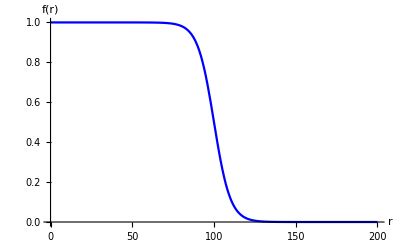

```mathematica
f0Plot=Plot[f0[r]/.{R->100,ϵ->10},{r,0,200},AxesLabel->{Style["r",16],Style["f(r)",16]},PlotStyle->Blue]
```

Pfenning & Ford form function f_pc(r), used to integrate over the energy density:

```mathematica
fpc[r_]:=Piecewise[{{1,r<R-Δ/2},{-1/Δ(r-R-Δ/2),R-Δ/2<r<R+Δ/2},{0,r>R+Δ/2}}];
fpc[r_]
```

Piecewise[{{1, r_<R-Δ/2}, {-(-R-Δ/2+r_)/Δ, R-Δ/2<r_<R+Δ/2}, {0, True}}]

Plot shows an approximate step function:

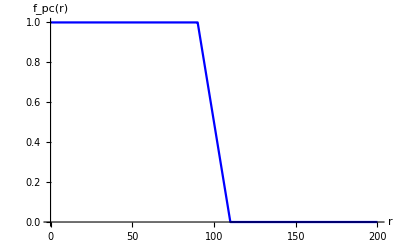

```mathematica
fpcPlot=Plot[fpc[r]/.{R->100,Δ->20},{r,0,200},AxesLabel->{Style["r",16],Style["f_pc(r)",16]},PlotStyle->Blue]
```

Δ and ϵ are related by:

```mathematica
Δ[σ]:=((1+Tanh[R σ]^2)^2)/(2σ Tanh[R σ])
```

Which can be approximated by Δ=2σ :

```mathematica
ΔPlot=Δ[σ]/.R->100
```

(Coth[100 σ] (1+Tanh[100 σ]^2)^2)/(2 σ)

Plot comparing Δ and 2/σ for R=100:

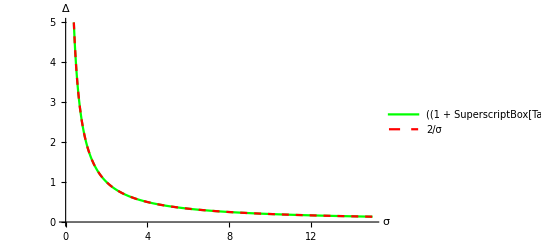

```mathematica
deltafunction=Plot[{ΔPlot,2/σ},{σ,0,15},PlotStyle->{Directive[Green,Thick],Directive[Red,Dashed]},PlotRange->{0,5},PlotLegends->{Style["(1 + SuperscriptBox[Tanh[R σ], 2])^2/(2  σ Tanh[R σ])",20],Style["2/σ",20]},AxesLabel->{Style["σ",20],Style["Δ",20]}]
```

Both lines follow the same curve, so clearly Δ=2/σ is a good approximation.

### Regularization function on h-dimension

Regularization function ξ_Gauss

```mathematica
ξgauss[h_]:=Exp[-h^2/h0^2]
```

Characteristic length for the non-compactified fifth dimension for ξ_Gauss

```mathematica
pergauss=Quantity[h0,"Meters"]
```

h0 m

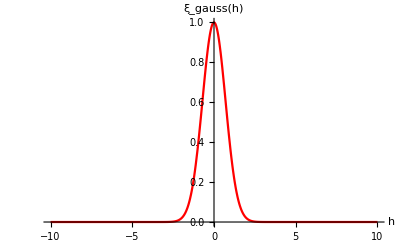

```mathematica
ξgaussPlot=Plot[ξgauss[h]/.h0->1,{h,-10,10},AxesLabel->{Style["h",16],Style["ξ_gauss(h)",16]},PlotRange->Full,PlotStyle->Red]
```

No regularization function (ξ_const=1):

```mathematica
ξconst[h_]:=1
```

Period of the compactified fifth dimension for ξ_const

```mathematica
perconst=Quantity[2,"PlanckLength"]
```

2 l_P

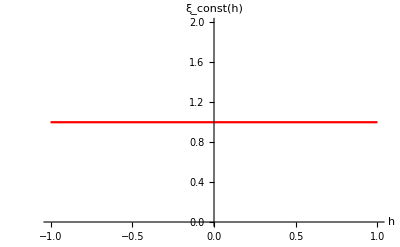

```mathematica
ξconstPlot=Plot[ξconst[h],{h,-1,1},AxesLabel->{Style["h",16],Style["ξ_const(h)",16]},PlotRange->Full,PlotStyle->Red]
```

## Metrics

### Original Alcubierre Warp Drive (Warp4D)

4D Alcubierre warp drive:

```mathematica
Warp4D={{-1 + v[t]^2 f[r[t, x, y, z]]^2 , 0, 
    0, -v[t] f[r[t, x, y, z]]}, {0, 1,
     0, 0}, {0, 0, 1, 0}, {-v[t] f[r[t, x, y, z]], 0, 0, 
    1}};
Warp4D//MatrixForm
```

(-1+f[r[t,x,y,z]]^2 v[t]^2 | 0 | 0 | -f[r[t,x,y,z]] v[t]
0 | 1 | 0 | 0
0 | 0 | 1 | 0
-f[r[t,x,y,z]] v[t] | 0 | 0 | 1)

### Alcubierre 5D Warp Drive (Warp 5D)

5D warp drive:

```mathematica
Warp5DBeta={{-1 + v[t]^2 f[r[t, x, y, z]]^2 ξ[h]^2, 0, 
    0, -v[t] f[r[t, x, y, z]] ξ[h], -α v[t] f[r[t, x, y, z]] ξ[h]}, {0, 1,
     0, 0, 0}, {0, 0, 1, 0, 0}, {-v[t] f[r[t, x, y, z]] ξ[h], 0, 0, 
    1, β}, {-α v[t] f[r[t, x, y, z]] ξ[h], 0, 
    0, β, γ^2}};
    Warp5DBeta//MatrixForm
```

(-1+f[r[t,x,y,z]]^2 v[t]^2 ξ[h]^2 | 0 | 0 | -f[r[t,x,y,z]] v[t] ξ[h] | -α f[r[t,x,y,z]] v[t] ξ[h]
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
-f[r[t,x,y,z]] v[t] ξ[h] | 0 | 0 | 1 | β
-α f[r[t,x,y,z]] v[t] ξ[h] | 0 | 0 | β | γ^2)

## Original 4D Alcubierre Warp Drive

We will begin with an example of the process: the original Alcubierre warp drive.

## Stating the Metric

### Coordinates

We will be using 4D Cartesian (t,x,y,z) and spherical (t,r,θ,ϕ) coordinates.  We will load in 4D Cartesian and spherical and define their coordinate transformation.

```mathematica
TNewCoordinates["Cartesian4D",Evaluate[Cartesian4D]]
```

Cartesian4D

```mathematica
TNewCoordinates["Spherical4D",Evaluate[Spherical4D]]
```

Spherical4D

```mathematica
TAddCoordTransformation["Cartesian4D"->"Spherical4D",Evaluate[trans4D]]
```

Cartesian4D

### The Metric

The metric we will be using is the original Alcubierre warp drive metric:

```mathematica
TShow@TNewMetric["Warp4D","Cartesian4D",Warp4D]
```

Warp4D:   g_μν^μν(,,txyz) = (-1+f[r]^2 v[t]^2 | 0 | 0 | -f[r] v[t]
0 | 1 | 0 | 0
0 | 0 | 1 | 0
-f[r] v[t] | 0 | 0 | 1)

The determinant of this metric is:

```mathematica
det4D=TVolumeElementSquared["Warp4D","Cartesian4D"]
```

-1

The corresponding line element is given by:

```mathematica
LineElement4D=TLineElement["Warp4D"]//Expand//(#[[1]]+#[[2]]+#[[3]]+Factor[#[[4]]+#[[5]]+#[[6]]])&
```

-𝕕t^2+𝕕x^2+𝕕y^2+(𝕕z-𝕕t f[r[t,x,y,z]] v[t])^2

## Determining the 4-velocity Along the Geodesic

### Lagrangian

The geodesic Lagrangian is:

```mathematica
TList@TCalcLagrangian["Warp4D"]
```

Warp4DLagrangian:
==L_^ | = | (ẋ)^2+(ẏ)^2+(ż)^2-2 f[r] ṫ ż v[t]+(ṫ)^2 (-1+f[r]^2 v[t]^2)

The Euler-Lagrange equations are:

```mathematica
TList@TCalcGeodesicFromLagrangian["Warp4D","Cartesian4D"]
```

Warp4DGeodesicFromLagrangian:
==0_t^t | = | ṫ (-ż+f[r] ṫ v[t]) (v[t] Inactivert Inactivef[r]r+f[r] Inactivev[t]t)-Inactive(-f[r] ż v[t]+ṫ (-1+f[r]^2 v[t]^2))λ
==0_x^x | = | ṫ v[t] (-ż+f[r] ṫ v[t]) Inactiverx Inactivef[r]r-Inactiveẋλ
==0_y^y | = | ṫ v[t] (-ż+f[r] ṫ v[t]) Inactivery Inactivef[r]r-Inactiveẏλ
==0_z^z | = | ṫ v[t] (-ż+f[r] ṫ v[t]) Inactiverz Inactivef[r]r-Inactive(ż-f[r] ṫ v[t])λ

The system of equations above can be solved by hand to give:

```mathematica
geo4D={1,0,0,v[t] f[r[t,x,y,z]] }
```

{1,0,0,f[r[t,x,y,z]] v[t]}

To check our solution, we we can plug it back into the system of equations:

```mathematica
(TGetComponents@TCalcGeodesicFromLagrangian["Warp4D","Cartesian4D"])/.{t'[λ_]->1,x'[λ_]->0,y'[λ_]->0,z'[λ_]->v[t[λ]] f[r[t[λ],x[λ],y[λ],z[λ]]]}/.r->rr//Activate
```

TGetComponents::UsingDefault: Using the default index configuration {1} and the default coordinate system "Cartesian4D".

{0,0,0,0}

This 4-velocity solves the system of equations.

### Geodesic 4-velocity

Thus, the 4-velocity along the geodesic is given by:

```mathematica
TShow@TNewTensor["Observer4D","Warp4D",{1},Evaluate[geo4D]]
```

Observer4D:   ⬚_μ^μ(,,txyz) = (1
0
0
f[r] v[t])

This means the warp bubble travels along the z-direction with spatial velocity v.

Let us check the nature of this 4-velocity is timelike:

```mathematica
geotype= (TGetComponents@TCalc["Warp4D"["μν"]."Observer4D"["μ"]."Observer4D"["ν"]])[[1]];
If[geotype==-1,Print["The 4-velocity is timelike"],If[geotype==1,Print["The 4-velocity is spacelike"],If[geotype==0,Print["The 4-velocity is lightlike (null)"],Print["Error"]]]]
```

TGetComponents::UsingDefault: Using the default index configuration {} and the default coordinate system "Cartesian4D".

The 4-velocity is timelike

## Calculating the Energy Density ρ

### Energy Density Expression

To find an expression for the energy density ρ, we must first solve the Einstein Equation by finding the Einstein tensor.

```mathematica
TCalcEinsteinTensor["Warp4D"]
```

Warp4DEinstein

In Cartesian coordinates, the expression for the energy density ρ is:

```mathematica
TList@TCalc["EnergyDensity4D","Warp4DEinstein"["μν"]."Observer4D"["μ"]."Observer4D"["ν"]/(k)]
```

EnergyDensity4D:
==⬚_^ | = | -(v[t]^2 (Inactiverx^2+Inactivery^2) (Inactivef[r]r)^2)/(4 k)

In spherical coordinates, the expression becomes:

```mathematica
ρ4D=TGetComponents["EnergyDensity4D", {}, "Spherical4D"][[1]]/.r->rr//FullSimplify[#,rr>=0]&
```

-(Sin[θ]^2 v[t]^2 f'[rr]^2)/(4 k)

We can see clearly from this expression that the energy density is always negative everywhere -- or more accurately, always non-positive everywhere.  Thus, the original Alcubierre warp drive violates the WEC.

### Extremizing the Energy Density

We wish to find the upper and lower limits on the energy density.  To do this, we must find the minimum and maximum values of the derivative of the form function f_0, which we will call (f')_- and (f')_+, respectively.   We also know that (f')_-<f'<(f')_+<0 since f is always decreasing.  We then use these to find the absolute maximum and minimum of f', which we’ll call f_max and f_min, respectively.

Using f=f_0, we can find (f')_- and (f')_+.  The expression for f' is:

```mathematica
df[r_]:=D[f0[r],r]//Factor//Simplify
df[r]
```

(Coth[R/ϵ] (-Sech[(r-R)/ϵ]^2+Sech[(r+R)/ϵ]^2))/(2 ϵ)

Let us first look at coth(R/ϵ).  We know R > ϵ, so let’s plot coth(x) for x ≥ 1:

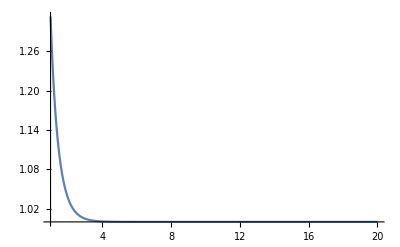

```mathematica
Plot[Coth[x],{x,1,20},PlotRange->Full]
```

We see that this function very quickly approaches 1 as the ratio R/ϵ increases.  Since the radius of the warp bubble, R, will be several times the thickness of the bubble ϵ (in both of our cases of a spaceship and a particle, we are using R=10ϵ), we can use the approximation coth(R/ϵ)≈1.

Now we look at (-sech^2((r-R)/ϵ)+sech^2((r+R)/ϵ)).  We know that sech^2(x)∈(0,1], and that R and ϵ will not have any effect on this range.  The plot will have a max at r=-R and a min at r=R, and these “humps” will be more narrow as ϵ increases.  Since we have the restriction r>0, we neglect the “hump” at r=-R:

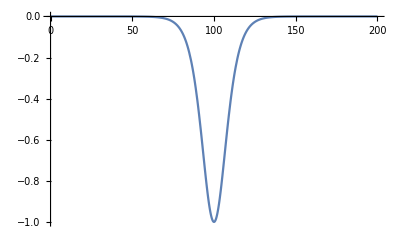

```mathematica
Plot[Sech[(x+R)/10]^2-Sech[(x-R)/10]^2/.R->100,{x,0,200},PlotRange->Full]
```

```mathematica
(-Sech[(r-R)/ϵ]^2+Sech[(r+R)/ϵ]^2)/.r->R
```

-1+Sech[(2 R)/ϵ]^2

Then, this factor has a minimum of -1+(sech((2 R)/ϵ))^2 when r=R.  Then we have -1<sech^2((r+R)/ϵ)-sech^2((r-R)/ϵ)<0.

Finally, we have that -1/(2ϵ)<f'<0, and 0<(f')^2<1/(4 ϵ^2).

Thus,

f_max=Max(|f|)=Max(|f_-|,|f_+|)=1
f_min=Min(|f|)=Min(|f_-|,|f_+|)=0
f'_max=Max(|f'|)=Max(|f'_-|,|f'_+|)=1/(2ϵ)
f'_min=Min(|f'|)=Min(|f'_-|,|f'_+|)=0

```mathematica
f0minus:=0
f0plus:=1
df0minus:=-1/(2ϵ)
df0plus:=0
f0max:=1
f0min:=0
df0max:=1/(2ϵ)
df0min:=0
```

Let' s rewrite the expression for the energy density in a simpler form:

```mathematica
ρ4Dbounds=-(Sin[θ]^2 v^2 f'^2)/(4k)
```

-(v^2 Sin[θ]^2 (f')^2)/(4 k)

Since the entire expression is negative, the lower limit will be determined by (f')_max

```mathematica
ρ4Dbounds/.f'->df0max
```

-(v^2 Sin[θ]^2)/(16 k ϵ^2)

And the upper limit by (f')_min

```mathematica
ρ4Dbounds/.f'->df0min
```

0

We can now see concretely that the energy density is everywhere non-positive.

### Expansion Plot

Let’s plot the expansion θ of a warp bubble travelling FTL with v=2, R=100m, and ϵ=10m.

The expansion of space around the warp bubble is given by θ=(z-ζ(t))/r v(t)f'(r):

```mathematica
expansion =(z-ζ[t])/r v[t]D[f[r],r]
```

(v[t] (z-ζ[t]) f'[r])/r

Let us plot θ for a warp bubble with R=100 m and ϵ=10 m travelling at v=2:

```mathematica
expansionplot=expansion/.v[t]->2*csub/.f->f0/.R->R0/.ϵ->ϵ0
```

(299792458 Coth[10] (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2) (z-ζ[t]))/r

We manually convert to Cartesian coordinates:

```mathematica
expansioncart=Refine[expansionplot/.r->rr[t,x,y,z]/.θ->ArcTan[√(x^2+y^2)/(z-ζ[t])]]/.ζ[t]->ζ0[t]/.t->0
```

(299792458 z Coth[10] (-1/10 Sech[1/10 (-100+√(x^2+y^2+z^2))]^2+1/10 Sech[1/10 (100+√(x^2+y^2+z^2))]^2))/(√(x^2+y^2+z^2))

And finally plot the expansion:

```mathematica
Plot3D[expansioncart/.x->0,{y,-150,150},{z,-150,150},PlotPoints->npoints,AxesLabel->{Style["y (m)",14], Style["z (m)",14],Style["θ (s^-1)",14]},PlotRange->Full,{ViewPoint->{0.8,1,0.4}}]
```

-Graphics3D-

### Energy Density Plots

Here we show our plots for the energy density ρ.

Let us create a 3-dimensional plot for a slice of the energy density ρ  with velocity v = 1. We will create the plot for a warp drive large enough to hold a spaceship with bubble radius R=100 m and thickness ϵ=10 m.

```mathematica
ρ4Dplot=ρ4D/.k->k4Dsub/.v->v0/.t->0/.f->f0/.{R->R0,ϵ->ϵ0,h0->1,rr->r}
```

-3.01×10^41 (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2)^2 Sin[θ]^2

Switch from spherical to Cartesian coordinates.

```mathematica
ρ4Dcart=Refine[ρ4Dplot/.r->rr[t,x,y,z]/.θ->ArcTan[√(x^2+y^2)/(z-ζ[t])]]/.ζ->ζ0/.t->0
```

-(3.01×10^41 (x^2+y^2) (-1/10 Sech[1/10 (-100+√(x^2+y^2+z^2))]^2+1/10 Sech[1/10 (100+√(x^2+y^2+z^2))]^2)^2)/((1+(x^2+y^2)/z^2) z^2)

The vertical axis will give the energy density ρ in units of Solar Masses/m^3, while the horizontal plane is plotted in polar coordinates (r,θ) with r and θ given in m and radians, respectively.  Since t^ and ϕ do not explicitly appear in the expression for ρ, the plot will show a slice of the energy density at an arbitrary moment in time and an arbitrary azimuthal angle.

```mathematica
RevolutionPlot3D[ρ4Dplot*conv/10^-6,{r,0,200},{θ,0,2 π},AxesLabel->{Style["x (m)",14], Style["y (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},PlotRange->Full,{ViewPoint->{5,3,1.3}}]
```

-Graphics3D-

We can now see that for this slice, ρ is non-positive everywhere.  Since ρ goes as v^2, the plot would be stretched along the vertical axis by a factor of v^2 for larger speeds.

Now we will create a 4-dimensional plot for a slice of the energy density ρ  with again velocity v=1 and arbitrary time t.  We will again use a warp bubble of radius R=100 m and thickness ϵ=10 m.  The plot will be coloured by ρ in units of M_☉/m^3.

```mathematica
densityplot4D=DensityPlot3D[ρ4Dcart*conv/10^-6,{x,-120,120},{y,-120,120},{z,-120,120},PlotRange->{Full,Full,Full,Automatic},ColorFunction->"BlueGreenYellow",OpacityFunction->Function[f,(1-f)^2],PlotPoints->npoints,PlotLegends->Placed[Automatic,Below,Labeled[#,"ρ (10^-6M_⊙/m^4)"]&],AxesLabel->{"x (m)","y (m)","z(m)","ρ"}]
```

-Graphics3D-

The warp bubble is shown to be a spherical shell with non-positive energy density everywhere in space.

## Calculating the Total Energy

To calculate the total energy, we must integrate over all space for a given moment in time.  Since ρ has no time dependence, we can integrate over an arbitrary moment in time.

```mathematica
Etot4D=Integrate[√Abs[det4D] ρ4D VolumeElement/.f->fpc/.r->rr,{rr,0,Infinity},{θ,0,π},{ϕ,0,2π}]//FullSimplify
```

-(π (12 R^2+Δ^2) v[t]^2)/(18 k Δ)

Restoring k_(4D)=(8π G_(4D))/c^4:

```mathematica
Etot4D/.k->k4Dsub
```

-(8.405×10^41 (12 R^2+Δ^2) v[t]^2)/Δ

Restoring k_(4D)=(8π G_(4D))/c^4, with G_(4D)=c=1, we recover the result from Pfenning & Ford:

```mathematica
Etot4D/.k->8π
```

-((12 R^2+Δ^2) v[t]^2)/(144 Δ)

### Spaceship Warp Drive

Let us calculate the total energy requirement for a warp drive large enough to fit a spaceship, with a warp bubble of radius R=100 m and thickness ϵ=10 m.

```mathematica
Etot4DShip=Etot4D/.R->Quantity[R0,"Meters"]/.Δ->2ϵ/.ϵ->Quantity[ϵ0,"Meters"]
```

((-(3010 π)/9 m) v[t]^2)/k

Convert to Joules by restoring k:

```mathematica
UnitConvert[Etot4DShip/.k->k4D/.v[t]->Quantity[v,"DimensionlessUnit"],"Joules"]
```

-5.06×10^45 v^2 J

Convert to kilograms by dividing by c^2:

```mathematica
UnitConvert[UnitConvert[Etot4DShip/.k->k4D/.v[t]->Quantity[v,"DimensionlessUnit"],"Joules"]/Quantity["SpeedOfLight"]^2,"Kilograms"]
```

-5.629×10^28 v^2 kg

Convert to Solar Masses:

```mathematica
UnitConvert[UnitConvert[Etot4DShip/.k->k4D/.v[t]->Quantity[v,"DimensionlessUnit"],"Joules"]/Quantity["SpeedOfLight"]^2,"SolarMass"]
```

-0.0283 v^2 M_☉

Therefore, the total energy requirement for a warp drive the size of a spaceship is -0.02831 v^2 M_☉.

### Particle Warp Drive

Let us now repeat this process for the total energy requirement for a warp drive small enough to fit a single particle, with a warp bubble of radius R=1 Angstroms and thickness ϵ=0.1 Angstroms.

```mathematica
Etot4DParticle=Etot4D/.R->Quantity[R1,"Angstroms"]/.Δ->2ϵ/.ϵ->Quantity[ϵ1,"Angstroms"]
```

((-10.5069 Å) v[t]^2)/k

Convert to Joules by restoring k:

```mathematica
UnitConvert[Etot4DParticle/.k->k4D/.v[t]->Quantity[v,"DimensionlessUnit"],"Joules"]
```

-5.05954×10^33 v^2 J

Convert to kilograms by dividing by c^2:

```mathematica
UnitConvert[UnitConvert[Etot4DParticle/.k->k4D/.v[t]->Quantity[v,"DimensionlessUnit"],"Joules"]/Quantity["SpeedOfLight"]^2,"Kilograms"]
```

-5.6295×10^16 v^2 kg

Convert to Solar Masses:

```mathematica
UnitConvert[UnitConvert[Etot4DParticle/.k->k4D/.v[t]->Quantity[v,"DimensionlessUnit"],"Joules"]/Quantity["SpeedOfLight"]^2,"SolarMass"]
```

-2.83117×10^-14 v^2 M_☉

The total energy requirement for a warp drive the size of a particle is -2.831×10^-14 v^2 M_☉.

### Pfenning & Ford Total Energy

Pfenning & Ford find another value for the total energy requirement that results from the quantum inequality.  They impose the condition Δ ≤ 10^2 v Planck lengths.  Let us confirm their calculation.  They begin by taking the following approximation of the expression for the total energy:

```mathematica
EtotPfenFord=(-v[t]^2)/12(R^2/Δ)
```

-(R^2 v[t]^2)/(12 Δ)

Then substituting a bubble radius R=100 m (using k=(k_(4D))/(8π), because Pfenning and Ford already account for 8π):

```mathematica
UnitConvert[UnitConvert[(EtotPfenFord/k/.k->k4D/(8π)/.R->Quantity[R0,"Meters"]/.Δ->Quantity[100 ,"PlanckLength"]*v[t])/.v[t]->Quantity[v,"DimensionlessUnit"],"Joules"]/Quantity["SpeedOfLight"]^2,"SolarMass"]
```

-3.49×10^32 v M_☉

This value is 9 orders of magnitude larger than the mass of the entire observable universe.

In an attempt to recover the result E<=-6.2×10^70 v L_Planck from Pfenning & Ford, we substitute R=100 m strait into EtotPfenFord:

```mathematica
UnitConvert[EtotPfenFord/.{R->Quantity[R0,"Meters"],Δ->Quantity[100 ,"PlanckLength"]*v[t]}/.v[t]->Quantity[v,"DimensionlessUnit"],"PlanckLength"]
```

-3.19×10^70 v l_P

We note that this result is approximately half of that found by Pfenning & Ford.  We presume this is likely due to a typo in the original paper.

A similar calculation for a bubble with radius R = 1 Angstrom yields:

```mathematica
UnitConvert[UnitConvert[(EtotPfenFord/k/.k->k4D/(8π)/.R->Quantity[R1,"Angstroms"]/.Δ->Quantity[100 ,"PlanckLength"]*v[t])/.v[t]->Quantity[v,"DimensionlessUnit"],"Joules"]/Quantity["SpeedOfLight"]^2,"SolarMass"]
```

-3.49×10^8 v M_☉

## 5D Alcubierre Warp Drive

We will now apply the process to a modified version of the Alcubierre metric in an attempt to minimize the energy requirements.

## Modifying the Metric

### Coordinates

We will be using 5D Cartesian (t,x,y,z,h) and spherical (t,r,θ,ϕ,h) coordinates.  We will load in 5D Cartesian and spherical coordinates and define their coordinate transformation.

```mathematica
TNewCoordinates["Cartesian5D",Evaluate[Cartesian5D]]
```

Cartesian5D

```mathematica
TNewCoordinates["Spherical5D",Evaluate[Spherical5D]]
```

Spherical5D

```mathematica
TAddCoordTransformation["Cartesian5D"->"Spherical5D",Evaluate[trans5D]]
```

Cartesian5D

### The Metric

The metric we will be modifying is the original Alcubierre warp drive metric.  To this metric we will be adding a fifth spacetime dimension -- the h-dimension, along with some additional parameters.  Our new 5D metric is represented in Cartesian coordinates as:

```mathematica
TShow@TNewMetric["Warp5DBeta","Cartesian5D",Warp5DBeta]
```

Warp5DBeta:   g_μν^μν(,,txyzh) = (-1+f[r]^2 v[t]^2 ξ[h]^2 | 0 | 0 | -f[r] v[t] ξ[h] | -α f[r] v[t] ξ[h]
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
-f[r] v[t] ξ[h] | 0 | 0 | 1 | β
-α f[r] v[t] ξ[h] | 0 | 0 | β | γ^2)

The determinant of this metric is:

```mathematica
det5DBeta=TVolumeElementSquared["Warp5DBeta"]
```

β^2-γ^2-(α-β)^2 f[r[t,x,y,z]]^2 v[t]^2 ξ[h]^2

The corresponding line element is:

```mathematica
linelement5DBeta=TLineElement["Warp5DBeta"]//Expand//(#[[1]]+#[[2]]+#[[3]]+Factor[#[[4]]+#[[7]]+#[[9]]]+Factor[#[[5]]+#[[8]]]+#[[6]])&
```

-𝕕t^2+𝕕x^2+𝕕y^2+𝕕h^2 γ^2+(𝕕z-𝕕t f[r[t,x,y,z]] v[t] ξ[h])^2+2 𝕕h (𝕕z β-𝕕t α f[r[t,x,y,z]] v[t] ξ[h])

## Determining the 4-velocity Along the Geodesic

### Lagrangian

The geodesic Lagrangian is:

```mathematica
TList@TCalcLagrangian["Warp5DBeta"]
```

Warp5DBetaLagrangian:
==L_^ | = | γ^2 (ḣ)^2+(ẋ)^2+(ẏ)^2+(ż)^2-2 f[r] ṫ ż v[t] ξ[h]+ḣ (2 β ż-2 α f[r] ṫ v[t] ξ[h])+(ṫ)^2 (-1+f[r]^2 v[t]^2 ξ[h]^2)

The Euler-Lagrange Equations are:

```mathematica
TList@TCalcGeodesicFromLagrangian["Warp5DBeta"]
```

Warp5DBetaGeodesicFromLagrangian:
==0_t^t | = | -ṫ ξ[h] (α ḣ+ż-f[r] ṫ v[t] ξ[h]) (v[t] Inactivert Inactivef[r]r+f[r] Inactivev[t]t)-Inactive(-ṫ+f[r] v[t] ξ[h] (-α ḣ-ż+f[r] ṫ v[t] ξ[h]))λ
==0_x^x | = | ṫ v[t] ξ[h] (-α ḣ-ż+f[r] ṫ v[t] ξ[h]) Inactiverx Inactivef[r]r-Inactiveẋλ
==0_y^y | = | ṫ v[t] ξ[h] (-α ḣ-ż+f[r] ṫ v[t] ξ[h]) Inactivery Inactivef[r]r-Inactiveẏλ
==0_z^z | = | ṫ v[t] ξ[h] (-α ḣ-ż+f[r] ṫ v[t] ξ[h]) Inactiverz Inactivef[r]r-Inactive(β ḣ+ż-f[r] ṫ v[t] ξ[h])λ
==0_h^h | = | f[r] ṫ v[t] (-α ḣ-ż+f[r] ṫ v[t] ξ[h]) Inactiveξ[h]h-Inactive(γ^2 ḣ+β ż-α f[r] ṫ v[t] ξ[h])λ

Solving by hand, we see the most general solution to the system is:

```mathematica
geo5Domega={1,0,0,v[t] f[r[t,x,y,z]] ξ[h]+(α ω)/(α^2-γ^2),-ω/(α^2-γ^2) }
```

{1,0,0,(α ω)/(α^2-γ^2)+f[r[t,x,y,z]] v[t] ξ[h],-ω/(α^2-γ^2)}

Where in our solution we have set α=β.

To check our solution, we we can plug it back into the system of equations:

```mathematica
(TGetComponents@TCalcGeodesicFromLagrangian["Warp5DBeta","Cartesian5D"])/.β->α/.{t'[λ_]->1,x'[λ_]->0,y'[λ_]->0,z'[λ_]->v[t[λ]] f[r[t[λ],x[λ],y[λ],z[λ]]] ξ[h[λ]]+(α ω)/(α^2-γ^2),h'[λ_]->-ω/(α^2-γ^2)}/.r->rr//Activate//FullSimplify
```

TGetComponents::UsingDefault: Using the default index configuration {1} and the default coordinate system "Cartesian5D".

{0,0,0,0,0}

We see that the 4-velocity greatly simplifies if we set ω = 0:

```mathematica
geo5D=geo5Domega/.ω->0
```

{1,0,0,f[r[t,x,y,z]] v[t] ξ[h],0}

### New Metric

Since we have set α = β in our solution, we must update our metric:

```mathematica
TShow@TNewMetric["Warp5D","Cartesian5D",Evaluate[Warp5DBeta/.β->α]]
```

Warp5D:   g_μν^μν(,,txyzh) = (-1+f[r]^2 v[t]^2 ξ[h]^2 | 0 | 0 | -f[r] v[t] ξ[h] | -α f[r] v[t] ξ[h]
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
-f[r] v[t] ξ[h] | 0 | 0 | 1 | α
-α f[r] v[t] ξ[h] | 0 | 0 | α | γ^2)

with determinant:

```mathematica
det5D=det5DBeta/.β->α
```

α^2-γ^2

and line element:

```mathematica
linelement5D=linelement5DBeta/.β->α//(#[[1]]+#[[2]]+#[[3]]+#[[4]]+#[[5]]+Factor[#[[6]]])&
```

-𝕕t^2+𝕕x^2+𝕕y^2+𝕕h^2 γ^2+2 𝕕h α (𝕕z-𝕕t f[r[t,x,y,z]] v[t] ξ[h])+(𝕕z-𝕕t f[r[t,x,y,z]] v[t] ξ[h])^2

### Geodesic 4-velocity

The 4-velocity along the geodesic is given by:

```mathematica
TShow@TNewTensor["Observer5D","Warp5D",{1},Evaluate[geo5D]]
```

Observer5D:   ⬚_μ^μ(,,txyzh) = (1
0
0
f[r] v[t] ξ[h]
0)

This means the warp bubble travels along the z-direction with spatial velocity v

Let us check the nature of this 4-velocity is timelike:

```mathematica
geotype= (TGetComponents@TCalc["Warp5D"["μν"]."Observer5D"["μ"]."Observer5D"["ν"]])[[1]];
If[geotype==-1,Print["The 4-velocity is timelike"],If[geotype==1,Print["The 4-velocity is spacelike"],If[geotype==0,Print["The 4-velocity is lightlike (null)"],Print["Error"]]]]
```

TGetComponents::UsingDefault: Using the default index configuration {} and the default coordinate system "Cartesian5D".

The 4-velocity is timelike

## Calculating the Energy Density (Generic ξ)

### Energy Density Expression

To find an expression for the energy density ρ, we must first solve the Einstein Equation by finding the Einstein tensor. (This may take a minute).

```mathematica
TCalcEinsteinTensor["Warp5D"]
```

Warp5DEinstein

In Cartesian coordinates, the expression for the energy density ρ is

```mathematica
TList@TCalc["EnergyDensity5D","Warp5DEinstein"["μν"]."Observer5D"["μ"]."Observer5D"["ν"]/(k)]
```

EnergyDensity5D:
==⬚_^ | = | (v[t]^2 (ξ[h]^2 (-((α-γ) (α+γ) (Inactiverx^2+Inactivery^2))+α^2 Inactiverz^2) (Inactivef[r]r)^2-2 α f[r] ξ[h] Inactiverz Inactivef[r]r Inactiveξ[h]h+f[r]^2 (Inactiveξ[h]h)^2))/(4 k (α-γ) (α+γ))

In spherical coordinates, ρ becomes:

```mathematica
ρ5D=TGetComponents["EnergyDensity5D", {}, "Spherical5D"][[1]]/.r->rr//FullSimplify[#,rr>=0]&
```

(v[t]^2 ((γ^2+(2 α^2-γ^2) Cos[2 θ]) ξ[h]^2 f'[rr]^2-4 α Cos[θ] f[rr] ξ[h] f'[rr] ξ'[h]+2 f[rr]^2 ξ'[h]^2))/(8 k (α-γ) (α+γ))

Unlike with the original Alcubierre metric, we cannot immediately tell if this expression violates the WEC.  We must now choose values and functions for our parameters and study the resulting expression.

### Extremizing the Energy Density

Before choosing values for our parameters, let us first try to extremize the expression for the energy density for arbitrary α, γ, ξ, and h_0.  We’ll start by writing the expression in a slightly simpler form:

v^2/(8k(α^2-γ^2))((γ^2+(2 α^2-γ^2)cos(2θ))ξ^2(f')^2-4αcos(θ)f ξ f'ξ'+2 f^2(ξ')^2),

which we will split into the following terms:

```mathematica
expr0:=v^2/(8k(α^2-γ^2))
expr1:=(γ^2+(2 α^2-γ^2)Cos[2θ])ξ^2(f')^2
expr2:=-4α Cos[θ]f ξ f'ξ'
expr3:=2 f^2(ξ')^2
```

From here, we see that if expr0 < 0, then to minimize ρ5D we need to maximize (expr1 + expr2 + expr3).  Similarly, if expr0 > 0, we need to minimize (expr1 + expr2 + expr3).   In the case of maximizing, if expr0 < 0 then we must minimize  (expr1 + expr2 + expr3), and if expr0 > 0, we must maximize (expr1 + expr2 + expr3).

Before moving on to the analysis, we must find the bounds on each of our functions and variables.

We identify the following parameter and variable boundaries:
α>0
γ>0
h_0>0
R>ϵ
v>0
0<=θ<=2π
r>=0

We must now find the bounds on the form function, regularization function, their derivatives, and their products.  For arbitrary function F, we will introduce the following notation:

F_-=Min(F)
F_+=Max(F)
F_max=Max(|F|)=Max(|F_-|,|F_+|)
F_min=Min(|F|)=Min(|F_-|,|F_+|)

We also note the following restrictions on f' and ξ:

(f')_-<f'<(f')_+<0 since f is always decreasing
ξ_-<ξ<ξ_+,ξ_+>=1 since ξ=1 inside the bubble

We are not able to find the maximum and minimum values for arbitrary ξ and ξ’ (we will do this for our specific choices for ξ below), but we will define
ξ_max=Max(|ξ|)=Max(|ξ_-|,|ξ_+|)
ξ_min=Min(|ξ|)=Min(|ξ_-|,|ξ_+|)
ξ'_max=Max(|ξ'|)=Max(|ξ'_-|,|ξ'_+|)
ξ'_min=Min(|ξ'|)=Min(|ξ'_-|,|ξ'_+|)

#### Bounds on f

By the nature of f, the bounds are clearly given by 0<=f<=1, and we have

f_max=Max(|f|)=Max(|f_-|,|f_+|)=1
f_min=Min(|f|)=Min(|f_-|,|f_+|)=0

```mathematica
f0minus:=0
f0plus:=1
f0max:=1
f0min:=0
```

#### Bounds on f'

We found the bounds on f' when extremizing ρ for the original 4D Alcubierre warp drive.  Since we are using the same f, these bounds remain the same for the 5D warp drive:

f'_max=Max(|f'|)=Max(|f'_-|,|f'_+|)=1/(2ϵ)
f'_min=Min(|f'|)=Min(|f'_-|,|f'_+|)=0

```mathematica
df0minus:=-1/(2ϵ)
df0plus:=0
df0max:=1/(2ϵ)
df0min:=0
```

#### Max/Min of expr1

We’ll now find the maximum and minimum of expr 1:

```mathematica
expr1
```

ξ^2 (γ^2+(2 α^2-γ^2) Cos[2 θ]) (f')^2

First, we see that cos(2θ) has a minimum of -1 and a maximum of 1.  At these extremum the factor (γ^2+(2 α^2-γ^2) Cos[2 θ]) becomes

```mathematica
(γ^2+(2 α^2-γ^2) Cos[2 θ])/.θ->π/2
```

-2 α^2+2 γ^2

or

```mathematica
(γ^2+(2 α^2-γ^2) Cos[2 θ])/.θ->0
```

2 α^2

We see that 2 α^2>2(γ^2-α^2) when γ^2<2 α^2 and  2 α^2<2(γ^2-α^2) when γ^2>2 α^2. Then we have four cases based on the following two expressions:

```mathematica
expr1a=expr1/.θ->π/2//FullSimplify
```

2 (-α^2+γ^2) ξ^2 (f')^2

```mathematica
expr1b=expr1/.θ->0//FullSimplify
```

2 α^2 ξ^2 (f')^2

To find the minimum and maximum of expr1, we need to consider several cases.

Case 1: γ^2>2 α^2

Since γ^2>2 α^2, then 0<α^2<(γ^2-α^2) and 0 < expr1b < expr1a, so the minimum will occur when ξ=ξ_min and f'=(f')_min=0 in expr1b (technically either expression gives the same result in this case since we have a factor of 0)

```mathematica
expr1Min1=expr1b/.{ξ->ξmin,f'->dfmin}
```

2 dfmin^2 α^2 ξmin^2

The maximum will occur when ξ=ξ_max and f'=(f')_max=0 in expr1a

```mathematica
expr1Max1=expr1a/.{ξ->ξmax,f'->dfmax}
```

2 dfmax^2 (-α^2+γ^2) ξmax^2

Case 2: γ^2=2 α^2

Since γ^2=2 α^2, then 0<α^2=(γ^2-α^2) and 0 < expr1b = expr1a, so the minimum will occur when ξ=ξ_min and f'=(f')_min=0 in either expression

```mathematica
expr1Min2=expr1b/.{ξ->ξmin,f'->dfmin}
```

2 dfmin^2 α^2 ξmin^2

The maximum will occur when ξ=ξ_max and f'=(f')_max=0 in either expression

```mathematica
expr1Max2=expr1b/.{ξ->ξmax,f'->dfmax}
```

2 dfmax^2 α^2 ξmax^2

Case 3: α^2<γ^2<α^2

If α^2>γ^2, then 0<(γ^2-α^2)<=α^2 and 0 < expr1a ≤ expr1b, so the minimum will occur when ξ=ξ_min and f'=(f')_min=0 in expr1a (really, either expression gives the same result in this case since we have a factor of 0)

```mathematica
expr1Min3=expr1a/.{ξ->ξmin,f'->dfmin}
```

2 dfmin^2 (-α^2+γ^2) ξmin^2

The maximum will occur when ξ=ξ_max and f'=(f')_max=0 in expr1b

```mathematica
expr1Max3=expr1b/.{ξ->ξmax,f'->dfmax}
```

2 dfmax^2 α^2 ξmax^2

#### Max/Min of expr2

We’ll now find the maximum and minimum of expr 2:

```mathematica
expr2
```

```mathematica
-4 f α ξ Cos[θ] f' ξ'
```

-4 f α ξ Cos[θ] f' ξ'

For the factor cos(θ), the max is 1 and the min is -1.  We can use this to make the sign arbitrary, and thus we want to maximize |4 f α ξ Cos[θ] f' ξ'|.

Then the maximum and minimum both occur when f,f',ξ,ξ' are all maximized, but we use cos(θ) to control the sign

```mathematica
expr2Max=expr2/.{θ->π,ξ->ξmax,ξ'->dξmax,f->fmax,f'->dfmax}
```

4 dfmax dξmax fmax α ξmax

Similarly, the minimum is

```mathematica
expr2Min=expr2/.{θ->0,ξ->ξmax,ξ'->dξmax,f->fmax,f'->dfmax}
```

-4 dfmax dξmax fmax α ξmax

#### Max/Min of expr3

We’ll now find the maximum and minimum of expr3:

```mathematica
expr3
```

2 f^2 (ξ')^2

Clearly, the minimum occurs when f and ξ’ are minimized:

```mathematica
expr3Min=expr3/.{ξ'->dξmin,f->fmin}
```

2 dξmin^2 fmin^2

and the maximum occurs when f and ξ’ are maximized:

```mathematica
expr3Max=expr3/.{ξ'->dξmax,f->fmax}
```

2 dξmax^2 fmax^2

#### Case 1: γ^2>2 α^2

If α^2<γ^2, then (α^2-γ^2)< 0 and exprA < 0.  Then, we must maximize (expr1 + expr2 + expr3) with the restriction γ^2>2 α^2:

```mathematica
ρmin1=expr0*(expr1Max1+expr2Max+expr3Max)//FullSimplify
```

(v^2 (dξmax^2 fmax^2+2 dfmax dξmax fmax α ξmax+dfmax^2 (-α^2+γ^2) ξmax^2))/(4 k (α^2-γ^2))

The minimum is negative.

To find the maximum we must minimize (expr1 + expr2 + expr3):

```mathematica
ρmax1=expr0*(expr1Min1+expr2Min+expr3Min)//Factor
```

(v^2 (dξmin^2 fmin^2-2 dfmax dξmax fmax α ξmax+dfmin^2 α^2 ξmin^2))/(4 k (α-γ) (α+γ))

The maximum is positive or negative, depending on the sign of the sum.

#### Case 2: γ^2=2 α^2

If γ^2=2 α^2, then (α^2-γ^2)< 0 and exprA < 0.  Then, we must maximize (expr1 + expr2 + expr3) with the restriction γ^2<2 α^2:

```mathematica
ρmin2=expr0*(expr1Max2+expr2Max+expr3Max)/.α->γ/(√2)//FullSimplify
```

-(v^2 (2 dξmax^2 fmax^2+2 √2 dfmax dξmax fmax γ ξmax+dfmax^2 γ^2 ξmax^2))/(4 k γ^2)

The minimum is negative.

To find the maximum we must minimize (expr1 + expr2 + expr3):

```mathematica
ρmax2=expr0*(expr1Min2+expr2Min+expr3Min)/.α->γ/(√2)//Factor
```

-(v^2 (2 dξmin^2 fmin^2-2 √2 dfmax dξmax fmax γ ξmax+dfmin^2 γ^2 ξmin^2))/(4 k γ^2)

The maximum is positive.

#### Case 3: α^2<γ^2<2 α^2

If α^2<γ^2, then (α^2-γ^2)< 0 and exprA < 0.  Then, we must maximize (expr1 + expr2 + expr3) with the restriction γ^2<2 α^2:

```mathematica
ρmin3=expr0*(expr1Max3+expr2Max+expr3Max)//FullSimplify
```

(v^2 (dξmax fmax+dfmax α ξmax)^2)/(4 k (α^2-γ^2))

The minimum is negative

To find the maximum we must minimize (expr1 + expr2 + expr3):

```mathematica
ρmax3=expr0*(expr1Min3+expr2Min+expr3Min)//Simplify
```

(v^2 (dξmin^2 fmin^2-2 dfmax dξmax fmax α ξmax+dfmin^2 (-α^2+γ^2) ξmin^2))/(4 k (α^2-γ^2))

The maximum is positive

## ξ_gauss(h)=exp(-h^2/h_0^2)

We will now consider the expression and visualizations for the energy density ρ and the expression and limits for the total energy E for regularization function ξ=ξ_Gauss.

### Extremizing the Energy Density

#### Bounds

Now that we have an expression for ξ, we can calculate the bounds on ξ and ξ’.  Let us start with ξ.  We know that for a Gaussian function, 0 < ξ < 1, and 0 < ξ^2<1.

```mathematica
ξgaussplus:=1
ξgaussminus:=0
```

From the plot of ξ, we can tell that ξ’ has negative, zero, and positive values.  We have the expression:

```mathematica
dξ:=D[ξgauss[h],h]//FullSimplify
dξ
```

-(2 ⅇ^(-h^2/h0^2) h)/h0^2

which looks like:

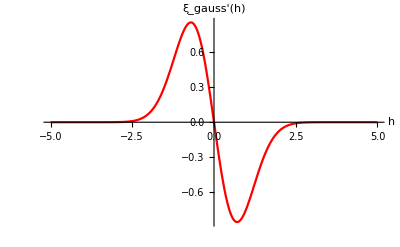

```mathematica
Plot[(-(2 ⅇ^(-h^2/h0^2) h)/h0^2/.h0->1),{h,-5,5},AxesLabel->{Style["h",16],Style["ξ_gauss'(h)",16]},PlotRange->Full,PlotStyle->Red]
```

Taking the second derivative, we get:

```mathematica
ddξ:=D[ξgauss[h],h,h]//FullSimplify
ddξ
```

-(2 ⅇ^(-h^2/h0^2) (-2 h^2+h0^2))/h0^4

We can find the maximum and minimum values of ξ’ by setting ξ’’=0

```mathematica
sol=Solve[ddξ==0,h]
```

{{h→-h0/(√2)},{h→h0/(√2)}}

```mathematica
dξgaussplus:=dξ/.h->sol[[1]][[1]][[2]]
dξgaussminus:=dξ/.h->sol[[2]][[1]][[2]]
dξgaussplus
dξgaussminus
```

(√(2/ⅇ))/h0

-(√(2/ⅇ))/h0

Since these extrema are equal in magnitude, this is clearly the magnitude of the absolute maximum as well.

From our expression for ξ’, it is clear to see that at h=0, ξ'=0:

```mathematica
dξ/.h->0
```

0

Finally, we have the absolute maxima and minima:

```mathematica
ξgaussmax:=1
ξgaussmin:=0
dξgaussmax:=(√(2/ⅇ))/h0
dξgaussmin:=0
```

#### Case 1: γ^2>2 α^2

```mathematica
ρgaussmin1=ρmin1/.{ξmax->ξgaussmax,dξmax->dξgaussmax,fmax->f0max,dfmax->df0max}//FullSimplify
```

(v^2 (-1+(4 ϵ (√(2 ⅇ) h0 α+2 ϵ))/(ⅇ h0^2 (α^2-γ^2))))/(16 k ϵ^2)

The minimum is negative.

```mathematica
ρgaussmax1=ρmax1/.{ξmax->ξgaussmax,dξmax->dξgaussmax,fmax->f0max,dfmax->df0max,fmin->f0min,dfmin->df0min}//Simplify//Factor
```

-(v^2 α)/(2 √(2 ⅇ) h0 k (α-γ) (α+γ) ϵ)

The maximum is positive.

#### Case 2: γ^2=2 α^2

```mathematica
ρgaussmin2=ρmin2/.{ξmax->ξgaussmax,dξmax->dξgaussmax,fmax->f0max,dfmax->df0max}//Simplify
```

-(v^2 (√ⅇ h0 γ+4 ϵ)^2)/(16 ⅇ h0^2 k γ^2 ϵ^2)

The minimum is negative.

```mathematica
ρgaussmax2=ρmax2/.{ξmax->ξgaussmax,dξmax->dξgaussmax,fmax->f0max,dfmax->df0max,fmin->f0min,dfmin->df0min}//Simplify//Factor
```

v^2/(2 √ⅇ h0 k γ ϵ)

The maximum is positive.

#### Case 3: α^2<γ^2<2 α^2

```mathematica
ρgaussmin3=ρmin3/.{ξmax->ξgaussmax,dξmax->dξgaussmax,fmax->f0max,dfmax->df0max}//Simplify
```

(v^2 ((√(2/ⅇ))/h0+α/(2 ϵ))^2)/(4 k (α^2-γ^2))

The minimum is negative.

```mathematica
ρgaussmax3=ρmax3/.{ξmax->ξgaussmax,dξmax->dξgaussmax,fmax->f0max,dfmax->df0max,fmin->f0min,dfmin->df0min}//Simplify//Factor
```

-(v^2 α)/(2 √(2 ⅇ) h0 k (α-γ) (α+γ) ϵ)

The maximum is positive.

### Energy Density Plots

Here we show our plots for the energy density ρ .  We will create the plot for a warp drive large enough to hold a spaceship with bubble radius R = 100 m and thickness ϵ = 10 m for all 3 cases outlined above.

We begin with the expression for ρ with form function given by f_0 and regularization function given by ξ_Gauss with v=1 and t=0:

```mathematica
k5Dgauss=QuantityMagnitude[k5D/.length->pergauss/.h0->1]
```

2.077×10^-43

```mathematica
ρgauss=ρ5D/.f->f0/.ξ->ξgauss/.k->k5Dgauss/.v->v0/.t->0
```

1/((α-γ) (α+γ))6.019×10^41 (1/4 ⅇ^(-(2 h^2)/h0^2) (γ^2+(2 α^2-γ^2) Cos[2 θ]) Coth[R/ϵ]^2 (-Sech[(-R+rr)/ϵ]^2/ϵ+Sech[(R+rr)/ϵ]^2/ϵ)^2+(2 ⅇ^(-(2 h^2)/h0^2) h α Cos[θ] Coth[R/ϵ]^2 (-Sech[(-R+rr)/ϵ]^2/ϵ+Sech[(R+rr)/ϵ]^2/ϵ) (-Tanh[(-R+rr)/ϵ]+Tanh[(R+rr)/ϵ]))/h0^2+(2 ⅇ^(-(2 h^2)/h0^2) h^2 Coth[R/ϵ]^2 (-Tanh[(-R+rr)/ϵ]+Tanh[(R+rr)/ϵ])^2)/h0^4)

Since this is an infinite dimension, we have substituted k=k_(5D)=k_(4D)×length, where the length is just some characteristic length, which we choose to be h_0.  We choose to substitute h_0=1 for the plot.

#### Case 1: γ^2>2 α^2

Let us create a 3-dimensional plot for a slice of the energy density ρ.

```mathematica
ρgauss1=ρgauss/.γ->√3/.α->1/.h0->1
```

-3.01×10^41 (1/4 ⅇ^(-2 h^2) (3-Cos[2 θ]) Coth[R/ϵ]^2 (-Sech[(-R+rr)/ϵ]^2/ϵ+Sech[(R+rr)/ϵ]^2/ϵ)^2+2 ⅇ^(-2 h^2) h Cos[θ] Coth[R/ϵ]^2 (-Sech[(-R+rr)/ϵ]^2/ϵ+Sech[(R+rr)/ϵ]^2/ϵ) (-Tanh[(-R+rr)/ϵ]+Tanh[(R+rr)/ϵ])+2 ⅇ^(-2 h^2) h^2 Coth[R/ϵ]^2 (-Tanh[(-R+rr)/ϵ]+Tanh[(R+rr)/ϵ])^2)

Let us substitute in values for R, ϵ:

```mathematica
ρgaussplot1=ρgauss1/.{R->R0,ϵ->ϵ0,rr->r}
```

-3.01×10^41 (1/4 ⅇ^(-2 h^2) (3-Cos[2 θ]) Coth[10]^2 (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2)^2+2 ⅇ^(-2 h^2) h Cos[θ] Coth[10]^2 (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2) (-Tanh[1/10 (-100+r)]+Tanh[(100+r)/10])+2 ⅇ^(-2 h^2) h^2 Coth[10]^2 (-Tanh[1/10 (-100+r)]+Tanh[(100+r)/10])^2)

The vertical axis will give the energy density ρ in units of Solar Masses/m^3, while the horizontal plane is plotted in polar coordinates (r,θ) with r and θ given in m and radians, respectively.  This is a slice of the energy density at h=0 for arbitrary t and ϕ and with velocity v=1.

```mathematica
RevolutionPlot3D[ρgaussplot1*conv/10^-6/.h->0,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full]
```

-Graphics3D-

Let us plot a different slice of the h-dimension, h=1:

```mathematica
RevolutionPlot3D[ρgaussplot1*conv/10^-6/.h->1,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full]
```

-Graphics3D-

Here we include an interactive plot that allows us to slide along the h-dimension:

```mathematica
Manipulate[RevolutionPlot3D[ρgaussplot1*conv/10^-6/. h->hh,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full,PlotRange->Full],{hh,-5,5}]
```

Let us also visualize the energy density in the fifth dimension by taking a slice of the h r-plane integrated over all of θ for arbitrary t,ϕ:

```mathematica
Plot3D[NIntegrate[ρgaussplot1*r/.r->rr/.h->hh,{θ,0,2π}]*conv/10^-6,{rr,0,150},{hh,-3,3},AxesLabel->{Style["r (m)",14], Style["h (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{3,4,-1.3}},PlotRange->Full]
```

-Graphics3D-

In this case, the energy density appears to be everywhere negative, with an excess of negative energy stored in the h-dimension.

Now we will create a 3-dimensional plot for a slice of the warp bubble coloured by the energy density ρ.  Again, we are considering a warp bubble moving at velocity v=1 at an arbitrary moment in time t and arbitrary azimuthal angle ϕ.  We will again use a warp bubble of radius R=100 m and thickness ϵ=10 m.  The plot will be done in Cartesian coordinates (X,z,h) in metres, where X is a combination of the x and y dimensions.

We begin by manually switching to Cartesian coordinates:

```mathematica
ρgausscart1=Refine[ρgaussplot1/.r->rr[t,x,y,z]/.θ->ArcTan[√(x^2+y^2)/(z-ζ[t])]/.{x->1/(√2)X,y->1/(√2)X},Element[X,Reals]]/.ζ->ζ0/.t->0
```

-3.01×10^41 (1/4 ⅇ^(-2 h^2) (3-Cos[2 ArcTan[Abs[X]/z]]) Coth[10]^2 (-1/10 Sech[1/10 (-100+√(X^2+z^2))]^2+1/10 Sech[1/10 (100+√(X^2+z^2))]^2)^2+(2 ⅇ^(-2 h^2) h Coth[10]^2 (-1/10 Sech[1/10 (-100+√(X^2+z^2))]^2+1/10 Sech[1/10 (100+√(X^2+z^2))]^2) (-Tanh[1/10 (-100+√(X^2+z^2))]+Tanh[1/10 (100+√(X^2+z^2))]))/(√(1+X^2/z^2))+2 ⅇ^(-2 h^2) h^2 Coth[10]^2 (-Tanh[1/10 (-100+√(X^2+z^2))]+Tanh[1/10 (100+√(X^2+z^2))])^2)

The plot will be coloured by ρ in units of Solar M_☉×10^-6/m^4. (This may take a few minutes).

```mathematica
densityplotgauss1=DensityPlot3D[ρgausscart1*conv/10^-6,{X,-120,120},{z,-120,120},{h,-5,5},PlotRange->{Full,Full,Full,Automatic},ColorFunction->"BlueGreenYellow",OpacityFunction->Function[f,(1-f)^2],PlotPoints->npoints,PlotLegends->Placed[Automatic,Below,Labeled[#,"ρ (10^-6M_⊙/m^4)"]&],AxesLabel->{"X (m)","z (m)","h(m)","ρ"}]
```

-Graphics3D-

#### Case 2: γ^2=2 α^2

To fit the case, let us substitute γ=√2, α=1:

```mathematica
ρgaussplot2=ρgauss/.γ->√2/.α->1/.{R->R0,ϵ->ϵ0,h0->1,rr->r}
```

-6.019×10^41 (1/2 ⅇ^(-2 h^2) Coth[10]^2 (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2)^2+2 ⅇ^(-2 h^2) h Cos[θ] Coth[10]^2 (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2) (-Tanh[1/10 (-100+r)]+Tanh[(100+r)/10])+2 ⅇ^(-2 h^2) h^2 Coth[10]^2 (-Tanh[1/10 (-100+r)]+Tanh[(100+r)/10])^2)

This is a slice of the energy density at h=0 for arbitrary t and ϕ and with velocity v=1.

```mathematica
RevolutionPlot3D[ρgaussplot2*conv/10^-6/.h->0,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full]
```

-Graphics3D-

Let us plot a different slice of the h-dimension, h=1:

```mathematica
RevolutionPlot3D[ρgaussplot2*conv/10^-6/.h->1,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full]
```

-Graphics3D-

Here we include an interactive plot that allows us to slide along the h-dimension:

```mathematica
Manipulate[RevolutionPlot3D[ρgaussplot2*conv/10^-6/. h->hh,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full],{hh,-5,5}]
```

Let us also visualize the energy density in the fifth dimension by taking a slice of the h r-plane integrated over all of θ for arbitrary t,ϕ:

```mathematica
Plot3D[NIntegrate[ρgaussplot2*r/.r->rr/.h->hh,{θ,0,2π}]*conv/10^-6,{rr,0,150},{hh,-3,3},AxesLabel->{Style["r (m)",14], Style["h (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{3,4,-1.3}},PlotRange->Full]
```

-Graphics3D-

In this case, the energy density appears to be everywhere negative, with an excess of negative energy stored in the h-dimension.

Now for the 3-dimensional slice coloured by ρ (This may take a few minutes):

```mathematica
ρgausscart2=Refine[ρgaussplot2/.r->rr[t,x,y,z]/.θ->ArcTan[√(x^2+y^2)/(z-ζ[t])]/.{x->1/(√2)X,y->1/(√2)X}/.v->v0/.ζ->ζ0/.t->0,Element[X,Reals]]/.ζ->ζ0/.t->0
```

-6.019×10^41 (1/2 ⅇ^(-2 h^2) Coth[10]^2 (-1/10 Sech[1/10 (-100+√(X^2+z^2))]^2+1/10 Sech[1/10 (100+√(X^2+z^2))]^2)^2+(2 ⅇ^(-2 h^2) h Coth[10]^2 (-1/10 Sech[1/10 (-100+√(X^2+z^2))]^2+1/10 Sech[1/10 (100+√(X^2+z^2))]^2) (-Tanh[1/10 (-100+√(X^2+z^2))]+Tanh[1/10 (100+√(X^2+z^2))]))/(√(1+X^2/z^2))+2 ⅇ^(-2 h^2) h^2 Coth[10]^2 (-Tanh[1/10 (-100+√(X^2+z^2))]+Tanh[1/10 (100+√(X^2+z^2))])^2)

```mathematica
densityplotgauss2=DensityPlot3D[ρgausscart2*conv/10^-6,{X,-120,120},{z,-120,120},{h,-5,5},PlotRange->{Full,Full,Full,Automatic},ColorFunction->"BlueGreenYellow",OpacityFunction->Function[f,(1-f)^2],PlotPoints->npoints,PlotLegends->Placed[Automatic,Below,Labeled[#,"ρ (10^-6M_⊙/m^4)"]&],AxesLabel->{"X (m)","z (m)","h(m)","ρ"}]
```

-Graphics3D-

#### Case 3: α^2<γ^2<=2 α^2

To fit the case, let us substitute γ=√(3/2), α=1:

```mathematica
ρgaussplot3=ρgauss/.γ->√(3/2)/.α->1/.{R->R0,ϵ->ϵ0,h0->1,rr->r}
```

-1.204×10^42 (1/4 ⅇ^(-2 h^2) (3/2+1/2 Cos[2 θ]) Coth[10]^2 (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2)^2+2 ⅇ^(-2 h^2) h Cos[θ] Coth[10]^2 (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2) (-Tanh[1/10 (-100+r)]+Tanh[(100+r)/10])+2 ⅇ^(-2 h^2) h^2 Coth[10]^2 (-Tanh[1/10 (-100+r)]+Tanh[(100+r)/10])^2)

This is a slice of the energy density at h=0 for arbitrary t and ϕ and with velocity v=1.

```mathematica
RevolutionPlot3D[ρgaussplot3*conv/10^-6/.h->0,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{2,5,1.3}},PlotRange->Full]
```

-Graphics3D-

Let us plot a different slice of the h-dimension, h=1:

```mathematica
RevolutionPlot3D[ρgaussplot3*conv/10^-6/.h->1,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full]
```

-Graphics3D-

Here we include an interactive plot that allows us to slide along the h-dimension:

```mathematica
Manipulate[RevolutionPlot3D[ρgaussplot3*conv/10^-6/. h->hh,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full],{hh,-5,5}]
```

Let us also visualize the energy density in the fifth dimension by taking a slice of the h r-plane integrated over all of θ for arbitrary t,ϕ:

```mathematica
Plot3D[NIntegrate[ρgaussplot3*r/.r->rr/.h->hh,{θ,0,2π}]*conv/10^-6,{rr,0,150},{hh,-3,3},AxesLabel->{Style["r (m)",14], Style["h (m)",14],Style["ρ (10^-6 M_⊙/m^4)",14]},{ViewPoint->{3,4,-1.3}},PlotRange->Full]
```

-Graphics3D-

In this case, the energy density appears to be everywhere negative, with an excess of negative energy stored in the h-dimension.

Now for the 3-dimensional slice coloured by ρ (This may take a few minutes):

```mathematica
ρgausscart3=Refine[ρgaussplot3/.r->rr[t,x,y,z]/.θ->ArcTan[√(x^2+y^2)/(z-ζ[t])]/.{x->1/(√2)X,y->1/(√2)X}/.v->v0/.ζ->ζ0/.t->0,Element[X,Reals]]/.ζ->ζ0/.t->0
```

-1.204×10^42 (1/4 ⅇ^(-2 h^2) (3/2+1/2 Cos[2 ArcTan[Abs[X]/z]]) Coth[10]^2 (-1/10 Sech[1/10 (-100+√(X^2+z^2))]^2+1/10 Sech[1/10 (100+√(X^2+z^2))]^2)^2+(2 ⅇ^(-2 h^2) h Coth[10]^2 (-1/10 Sech[1/10 (-100+√(X^2+z^2))]^2+1/10 Sech[1/10 (100+√(X^2+z^2))]^2) (-Tanh[1/10 (-100+√(X^2+z^2))]+Tanh[1/10 (100+√(X^2+z^2))]))/(√(1+X^2/z^2))+2 ⅇ^(-2 h^2) h^2 Coth[10]^2 (-Tanh[1/10 (-100+√(X^2+z^2))]+Tanh[1/10 (100+√(X^2+z^2))])^2)

```mathematica
densityplotgauss3=DensityPlot3D[ρgausscart3*conv/10^-6,{X,-120,120},{z,-120,120},{h,-5,5},PlotRange->{Full,Full,Full,Automatic},ColorFunction->"BlueGreenYellow",OpacityFunction->Function[f,(1-f)^2],PlotPoints->npoints,PlotLegends->Placed[Automatic,Below,Labeled[#,"ρ (10^-6M_⊙/m^4)"]&],AxesLabel->{"X (m)","z (m)","h(m)","ρ"}]
```

-Graphics3D-

### Calculating the Total Energy

To calculate the total energy, we must integrate over all spatial dimensions and the h-dimension for a given moment in time.  Since there is no time dependence in the expression for the energy density, the integration is done for an arbitrary moment in time.  We will substitute ξ=ξ_gauss before the integration.  Since h is a non-compactified dimension, we will integrate over the range -∞ to ∞. (This may take a minute).

```mathematica
Egauss=√Abs[det5D]*Integrate[ρ5D VolumeElement/.f->fpc/.ξ->ξgauss/.r->rr,{rr,0,Infinity},{θ,0,π},{ϕ,0,2π},{h,-Infinity,Infinity},Assumptions->{h0>0,α>0,γ>0,0<Δ<R}]//Simplify
```

-(π^(3/2) (10 h0^2 (α^2-2 γ^2) (12 R^2+Δ^2)+3 Δ (-40 R^3+20 R^2 Δ-10 R Δ^2+Δ^3)) √Abs[α^2-γ^2] v[t]^2)/(360 √2 h0 k (α-γ) (α+γ) Δ)

Let us analyze this expression to see what choice in parameters will result in positive total energy.  Let us rewrite this as

-(√(π^3/2)√(|α^2-γ^2|)v^2)/(360k (α^2-γ^2)h_0 Δ)(10 h_0^2(α^2-2 γ^2)(12 R^2+Δ^2)+3Δ(-40 R^3+20 R^2 Δ-10 RΔ^2+Δ^3))

```mathematica
exprA:=-(√(π^3/2)√Abs[α^2-γ^2] v^2)/(360k(α^2-γ^2)Subscript[h, 0] Δ)
exprB:=10 Subscript[h, 0]^2(α^2-2 γ^2)(12 R^2+Δ^2)
exprC:=3Δ(-40 R^3+20 R^2 Δ-10 RΔ^2+Δ^3)
```

The term in front -(√(π/2)√(|α^2-γ^2|)v^2)/(360k (α^2-γ^2)h_0 Δ) is negative for a timelike dimension (α^2>γ^2) and positive for a spacelike dimension (α^2<γ^2).  We thus need to analyze when the two terms in the brackets are negative, positive, or zero for each case of a timelike or spacelike dimension.  We see that the first term 10 h_0^2(α^2-2 γ^2)(12 R^2+Δ^2)is negative only when α^2<2 γ^2 , and that it disappears entirely -- hence reducing the total energy -- when α^2=2 γ^2; however, the second term 3Δ(-40 R^3+20 R^2 Δ-10 RΔ^2+Δ^3)is less obvious.

#### Minimizing the term 3Δ(-40 R^3+20 R^2 Δ-10R Δ^2+Δ^3)

Let us visualize the cubic expression -40 R^3+20 R^2 Δ-10 RΔ^2+Δ^3 with a plot:

```mathematica
cubic:=-40 R^3+20 R^2 Δ-10 R Δ^2+Δ^3
Plot3D[{cubic,0},{R,-10,10},{Δ,-10,10},PlotRange->All]
```

-Graphics3D-

We see that the cubic expression does indeed have regions where it is negative.  Let us find for which values of R this cubic expression is negative:

```mathematica
Reduce[cubic<0,R]
```

(Δ<0&&R>Root[-Δ^3+10 Δ^2 #1-20 Δ #1^2+40 #1^3&,1])||(Δ==0&&R>0)||(Δ>0&&R>Root[-Δ^3+10 Δ^2 #1-20 Δ #1^2+40 #1^3&,1])

To satisfy our restrictions on Δ and R, we see that our expression is negative for values of R>Root[-Δ^3+10 Δ^2 R-20 Δ R^2+40 R^3].  Let us solve for this root using the cubic formula (Cardano’s formula) :

```mathematica
cubicformula:=((-b^3/(27 a^3)+(b c)/(6 a^2)-d/(2 a))+√((-b^3/(27 a^3)+(b c)/(6 a^2)-d/(2 a))^2+(c/(3 a)-b^2/(9 a^2))^3))^(1/3)+((-b^3/(27 a^3)+(b c)/(6 a^2)-d/(2 a))-√((-b^3/(27 a^3)+(b c)/(6 a^2)-d/(2 a))^2+(c/(3 a)-b^2/(9 a^2))^3))^(1/3)-b/(3 a)
```

```mathematica
cubesol=cubicformula/.{a->-40,b->20Δ,c->-10 Δ^2,d->Δ^3}//Simplify
```

1/30 (5+5^(2/3) (-4+6 √6)^(1/3)-5^(2/3) (4+6 √6)^(1/3)) Δ

```mathematica
N[cubesol/Δ,20]
```

0.12273108466863161349

We see the root is ~0.1227Δ, and therefore our expression is negative when R > 0.1227Δ ⇒ R > 0.2454ϵ.  Since the radius of the bubble must be larger than the thickness (R > ϵ), this condition is always satisfied and this term is always negative.

#### Case 1: α^2<γ^2

We note there is only 1 case in which the total energy is positive: α^2<γ^2.  In this case, exprA > 0, exprB < 0, and exprC < 0.

|A|(-|B|-|C|)
=-|A|(|B|+|C|)

This results in a total energy that is always negative:

```mathematica
Refine[Egauss,Assumptions->{α^2<γ^2,0<Δ<R}]//Simplify
```

-(π^(3/2) √(-α^2+γ^2) (10 h0^2 (α^2-2 γ^2) (12 R^2+Δ^2)+3 Δ (-40 R^3+20 R^2 Δ-10 R Δ^2+Δ^3)) v[t]^2)/(360 √2 h0 k (α-γ) (α+γ) Δ)

Spaceship Warp Drive

Let us calculate the total energy requirement for a warp drive large enough to fit a spaceship, with a warp bubble of radius R=100 m and thickness ϵ=10 m for α=γ/(√2) and arbitrary positive γ.

```mathematica
EgaussShip1a=Refine[Egauss/.R->Quantity[R0,"Meters"]/.Δ->2ϵ/.ϵ->Quantity[ϵ0,"Meters"]/.h0->Quantity[h0,"Meters"]/.α->γ/(√2),Assumptions->γ>0]//FullSimplify
```

((-(909800 π^(3/2))/(3 h0) m^2+γ^2 (-1505/6 h0 π^(3/2) m^2)) v[t]^2)/(k γ)

Note: h0 must be in m for units to work out.

Restoring the k_(5D) factor, we get a total energy in Joules:

```mathematica
EgaussShip1=UnitConvert[EgaussShip1a/.k->k5D/.length->pergauss/.{v[t]->Quantity[v,"DimensionlessUnit"],γ->Quantity[γ,"DimensionlessUnit"]},"Joules"]//FullSimplify
```

(-(8.132×10^48 v^2)/(h0^2 γ)-6.726×10^45 v^2 γ) J

Or in Solar Masses:

```mathematica
UnitConvert[EgaussShip1/Quantity["SpeedOfLight"]^2,"SolarMass"]//FullSimplify
```

(-(45.5 v^2)/(h0^2 γ)-0.0376 v^2 γ) M_☉

Therefore, the total energy requirement for a warp drive the size of a spaceship for arbitrary γ is (-(45.5 v^2)/(h0^2 γ)-0.0376 v^2 γ) ("M")_("☉").

This energy requirement is clearly negative but it may be made relatively small for chosen v,γ,h_0.  The simplest choice for these parameters is γ=1⟹α=1/(√2),h_0=1, resulting in:

```mathematica
UnitConvert[EgaussShip1/Quantity["SpeedOfLight"]^2,"SolarMass"]/.{γ->1,h0->1}
```

-45.5 v^2 M_☉

Or in kilograms:

```mathematica
UnitConvert[EgaussShip1/Quantity["SpeedOfLight"]^2,"Kilograms"]/.{γ->1,h0->1}
```

-9.055×10^31 v^2 kg

Using instead γ=Λ and h_0=1/Λ:

```mathematica
UnitConvert[EgaussShip1/Quantity["SpeedOfLight"]^2,"SolarMass"]/.{γ->QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]],h0->1/QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]]}
```

-5.×10^-51 v^2 M_☉

In kilograms:

```mathematica
UnitConvert[EgaussShip1/Quantity["SpeedOfLight"]^2,"Kilograms"]/.{γ->QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]],h0->1/QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]]}
```

-1.×10^-20 v^2 kg

Particle Warp Drive

Let us now repeat this process for the total energy requirement for a warp drive small enough to fit a single particle, with a warp bubble of radius R=1 Angstroms and thickness ϵ=0.1 Angstroms for α=γ/(√2) and arbitrary positive γ.

```mathematica
EgaussParticle1a=Refine[Egauss/.R->Quantity[R1,"Angstroms"]/.Δ->2ϵ/.ϵ->Quantity[ϵ1,"Angstroms"]/.h0->Quantity[h0,"Angstroms"]/.α->γ/(√2),Assumptions->γ>0]//FullSimplify
```

((-1.68869/h0 Å^2+γ^2 (-13.9672 h0 Å^2)) v[t]^2)/(k γ)

Restoring the k_(5D) factor and converting to Joules:

```mathematica
EgaussParticle1=UnitConvert[EgaussParticle1a/.k->k5D/.length->pergauss/.{γ->Quantity[γ,"DimensionlessUnit"],v[t]->Quantity[v,"DimensionlessUnit"]},"Joules"]//FullSimplify
```

(-(8.1318×10^22 v^2)/(h0^2 γ)-6.72585×10^23 v^2 γ) J

Then to solar masses:

```mathematica
UnitConvert[EgaussParticle1/Quantity["SpeedOfLight"]^2,"SolarMass"]//FullSimplify
```

(-(4.55032×10^-25 v^2)/(h0^2 γ)-3.76359×10^-24 v^2 γ) M_☉

Or, more practically, kilograms:

```mathematica
UnitConvert[EgaussParticle1/Quantity["SpeedOfLight"]^2,"Kilograms"]//FullSimplify
```

(-(904785. v^2)/(h0^2 γ)-7.48352×10^6 v^2 γ) kg

Therefore, the total energy requirement for a warp drive the size of a particle is (-(904785. v^2)/(h0^2 γ)-7.48352×10^6 v^2 γ) "kg".  
This energy requirement is negative and it is relatively small, even for arbitrary v,γ,h_0.  The simplest choice for these parameters is again γ=1⟹α=1/(√2),h_0=1, resulting in:

```mathematica
UnitConvert[EgaussParticle1/Quantity["SpeedOfLight"]^2,"SolarMass"]/.{γ->1,h0->1}
```

-4.21862×10^-24 v^2 M_☉

```mathematica
UnitConvert[EgaussParticle1/Quantity["SpeedOfLight"]^2,"Kilograms"]/.{γ->1,h0->1}
```

-8.3883×10^6 v^2 kg

Using γ = Λ and h_0=1/Λ:

```mathematica
UnitConvert[EgaussParticle1/Quantity["SpeedOfLight"]^2,"SolarMass"]/.{γ->QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]],h0->1/QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]]}
```

-4.66411×10^-76 v^2 M_☉

In kilograms:

```mathematica
UnitConvert[EgaussParticle1/Quantity["SpeedOfLight"]^2,"Kilograms"]/.{γ->QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]],h0->1/QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]]}
```

-9.27411×10^-46 v^2 kg

## ξ_const(h)=1

We will now consider the expression and visualizations for the energy density ρ and the expression and limits for the total energy E for regularization function ξ=ξ_const=1.

### Extremizing the Energy Density

#### Bounds

Now that we have an expression for ξ, we can calculate the bounds on ξ and ξ’.  We know that since ξ=1, then ξ_-=ξ_+=ξ_min=ξ_max=1, and ξ'_-=ξ'_+=ξ'_min=ξ'_max=0.

```mathematica
ξconstsub:=1
dξconstsub:=0
```

#### Case 1: γ^2>2 α^2

```mathematica
ρconstmin1=ρmin1/.{ξmax->ξconstsub,dξmax->dξconstsub,fmax->f0max,dfmax->df0max}//Simplify
```

-v^2/(16 k ϵ^2)

The minimum is negative.

```mathematica
ρconstmax1=ρmax1/.{ξmax->ξconstsub,dξmax->dξconstsub,fmax->f0max,dfmax->df0max,fmin->f0min,dfmin->df0min}//Simplify//Factor
```

0

The maximum is 0.

#### Case 2: γ^2=2 α^2

```mathematica
ρconstmin2=ρmin2/.{ξmax->ξconstsub,dξmax->dξconstsub,fmax->f0max,dfmax->df0max}//Simplify
```

-v^2/(16 k ϵ^2)

The minimum is negative.

```mathematica
ρconstmax2=ρmax2/.{ξmax->ξconstsub,dξmax->dξconstsub,fmax->f0max,dfmax->df0max,fmin->f0min,dfmin->df0min}//Simplify//Factor
```

0

The maximum is 0.

#### Case 3: α^2<γ^2<=2 α^2 (corresponding to a spacelike 5th dimension)

```mathematica
ρconstmin3=ρmin3/.{ξmax->ξconstsub,dξmax->dξconstsub,fmax->f0max,dfmax->df0max}//Simplify
```

(v^2 α^2)/(16 k (α^2-γ^2) ϵ^2)

The minimum is negative

```mathematica
ρconstmax3=ρmax3/.{ξmax->ξconstsub,dξmax->dξconstsub,fmax->f0max,dfmax->df0max,fmin->f0min,dfmin->df0min}//Simplify//Factor
```

0

The maximum is 0.

### Energy Density Plots

Here we show our plots for the energy density ρ .  We will create the plot for a warp drive large enough to hold a spaceship with bubble radius R = 100 m and thickness ϵ = 10 m for all 3 cases outlined above.

We begin with the expression for ρ with form function given by f_0 and regularization function given by ξ_Gauss with v=1 and t=0:

```mathematica
k5Dconst=QuantityMagnitude[k5D/.length->perconst]
```

6.713×10^-78

```mathematica
ρconst=ρ5D/.f->f0/.ξ->ξconst/.k->k5Dconst/.v->v0/.t->0
```

(4.655×10^75 (γ^2+(2 α^2-γ^2) Cos[2 θ]) Coth[R/ϵ]^2 (-Sech[(-R+rr)/ϵ]^2/ϵ+Sech[(R+rr)/ϵ]^2/ϵ)^2)/((α-γ) (α+γ))

Since this is a compactified dimension, we have substituted k=k_(5D)=k_(4D)×length, where the length is the period of the compactified dimension (h_0), which we have chosen to be 2 Planck lengths.

#### Case 1: γ^2>2 α^2

To fit the case, let us substitute γ=√3, α=1:

```mathematica
ρconstplot1=ρconst/.γ->√3/.α->1/.{R->R0,ϵ->ϵ0,h0->1,rr->r}
```

-2.328×10^75 (3-Cos[2 θ]) (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2)^2

As before, the vertical axis will give the energy density ρ in units of Solar Masses/m^3, while the horizontal plane is plotted in polar coordinates (r,θ) with r and θ given in m and radians, respectively.  This is a slice of the energy density for arbitrary t, h, and ϕ, and with velocity v=1.

```mathematica
RevolutionPlot3D[ρconstplot1*conv/10^26,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^26 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full]
```

-Graphics3D-

In this case, the energy density appears entirely negative.

Now we will create a 3-dimensional plot for a slice of the warp bubble coloured by the energy density ρ.  Again, we are considering a warp bubble moving at velocity v=1 at an arbitrary moment in time t and arbitrary azimuthal angle ϕ.  We will again use a warp bubble of radius R=100 m and thickness ϵ=10 m.  The plot will be done in Cartesian coordinates (X,z,h) in metres, where X is a combination of the x and y dimensions.

We begin by manually switching to Cartesian coordinates :

```mathematica
ρconstcart1=Refine[ρconstplot1/.r->rr[t,x,y,z]/.θ->ArcTan[√(x^2+y^2)/(z-ζ[t])]/.{x->1/(√2)X,y->1/(√2)X},Element[X,Reals]]/.ζ->ζ0/.t->0
```

-2.328×10^75 (3-Cos[2 ArcTan[Abs[X]/z]]) (-1/10 Sech[1/10 (-100+√(X^2+z^2))]^2+1/10 Sech[1/10 (100+√(X^2+z^2))]^2)^2

The plot will be coloured by ρ in units of Solar M_☉×10^-6/m^4. (This may take a few minutes).

```mathematica
densityplotconst1=DensityPlot3D[ρconstcart1*conv/10^26,{X,-120,120},{z,-120,120},{h,-5,5},PlotRange->{Full,Full,Full,Automatic},ColorFunction->"BlueGreenYellow",OpacityFunction->Function[f,(1-f)^2],PlotPoints->npoints,PlotLegends->Placed[Automatic,Below,Labeled[#,"ρ (10^26M_⊙/m^4)"]&],AxesLabel->{"X (m)","z (m)","h(m)","ρ"}]
```

-Graphics3D-

#### Case 2: γ^2=2 α^2

To fit the case, let us substitute γ=√2, α=1:

```mathematica
ρconstplot2=ρconst/.γ->√2/.α->1/.{R->R0,ϵ->ϵ0,h0->1,rr->r}
```

-9.311×10^75 (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2)^2

This is a slice of the energy density for arbitrary t, h, and ϕ, and with velocity v=1.

```mathematica
RevolutionPlot3D[ρconstplot2*conv/10^26/.h->0,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^26 M_⊙/m^4)",14]},{ViewPoint->{5,3,1.3}},PlotRange->Full]
```

-Graphics3D-

In this case, the energy density appears entirely negative.

And for the 3-dimensional plot coloured by ρ:

```mathematica
ρconstcart2=Refine[ρconstplot2/.r->rr[t,x,y,z]/.θ->ArcTan[√(x^2+y^2)/(z-ζ[t])]/.{x->1/(√2)X,y->1/(√2)X}/.v->v0/.ζ->ζ0/.t->0,Element[X,Reals]]/.ζ->ζ0/.t->0
```

-9.311×10^75 (-1/10 Sech[1/10 (-100+√(X^2+z^2))]^2+1/10 Sech[1/10 (100+√(X^2+z^2))]^2)^2

```mathematica
densityplotconst2=DensityPlot3D[ρconstcart2*conv/10^26,{X,-120,120},{z,-120,120},{h,-5,5},PlotRange->{Full,Full,Full,Automatic},ColorFunction->"BlueGreenYellow",OpacityFunction->Function[f,(1-f)^2],PlotPoints->npoints,PlotLegends->Placed[Automatic,Below,Labeled[#,"ρ (10^26M_⊙/m^4)"]&],AxesLabel->{"X (m)","z (m)","h(m)","ρ"}]
```

-Graphics3D-

#### Case 3: α^2<γ^2<=2 α^2

To fit the case, let us substitute γ=√(3/2), α=1:

```mathematica
ρconstplot3=ρconst/.γ->√(3/2)/.α->1/.{R->R0,ϵ->ϵ0,h0->1,rr->r}
```

-9.311×10^75 (3/2+1/2 Cos[2 θ]) (-1/10 Sech[1/10 (-100+r)]^2+1/10 Sech[(100+r)/10]^2)^2

This is a slice of the energy density for arbitrary t, h, and ϕ, and with velocity v=1.

```mathematica
RevolutionPlot3D[ρconstplot3*conv/10^26,{r,0,200},{θ,0,2 π},AxesLabel->{Style["X (m)",14], Style["z (m)",14],Style["ρ (10^26 M_⊙/m^4)",14]},{ViewPoint->{2,5,1.3}},PlotRange->Full]
```

-Graphics3D-

In this case, the energy density appears entirely negative.

And for the 3-dimensional plot coloured by ρ:

```mathematica
ρconstcart3=Refine[ρconstplot3/.r->rr[t,x,y,z]/.θ->ArcTan[√(x^2+y^2)/(z-ζ[t])]/.{x->1/(√2)X,y->1/(√2)X}/.v->v0/.ζ->ζ0/.t->0,Element[X,Reals]]/.ζ->ζ0/.t->0
```

-9.311×10^75 (3/2+1/2 Cos[2 ArcTan[Abs[X]/z]]) (-1/10 Sech[1/10 (-100+√(X^2+z^2))]^2+1/10 Sech[1/10 (100+√(X^2+z^2))]^2)^2

```mathematica
densityplotconst3=DensityPlot3D[ρconstcart3*conv/10^26,{X,-120,120},{z,-120,120},{h,-5,5},PlotRange->{Full,Full,Full,Automatic},ColorFunction->"BlueGreenYellow",OpacityFunction->Function[f,(1-f)^2],PlotPoints->npoints,PlotLegends->Placed[Automatic,Below,Labeled[#,"ρ (10^26M_⊙/m^4)"]&],AxesLabel->{"X (m)","z (m)","h(m)","ρ"}]
```

-Graphics3D-

### Calculating the Total Energy

To calculate the total energy, we must integrate over all spatial dimensions and the h-dimension for a given moment in time.  Since there is no time dependence in the expression for the energy density, the integration is done for an arbitrary moment in time.  Since h is a compactified dimension, we will integrate over the range -1 to 1 (which is a period of 2 planck lengths, the characteristic length we have chosen for the dimension).

```mathematica
Econst=√Abs[det5D]*Integrate[ρ5D VolumeElement/.f->fpc/.ξ->ξconst/.r->rr,{rr,0,Infinity},{θ,0,π},{ϕ,0,2π},{h,-1,1},Assumptions->{α>0,γ>0,0<Δ<R}]
```

-(π (α^2-2 γ^2) (12 R^2+Δ^2) √Abs[α^2-γ^2] v[t]^2)/(18 k (α^2-γ^2) Δ)

We will again split this expression up into smaller terms to analyze where the total energy is positive or negative.  We will start by rewriting the total energy as

-(π  (12 R^2+Δ^2) √Abs[α^2-γ^2] v[t]^2)/(18 k  Δ)(α^2-2 γ^2)/(α^2-γ^2)=D(E/F)

```mathematica
exprD:=-(π(12 R^2+Δ^2) √Abs[α^2-γ^2] v[t]^2)/(18k Δ)
exprE:=(α^2-2 γ^2) 
exprF:=(α-γ) (α+γ)
```

exprD is clearly always negative, but the sign of exprE and exprF depend on the choice in α and γ.  We note there is only 1 case in which the total energy is positive:

#### Case 1: α^2<γ^2

In this case, exprD < 0, exprB < 0, and exprC < 0.

-(|D|)((-|E|)/(-|F|))
=-|D|((|E|)/(|F|))

This results in a total energy that is always negative:

```mathematica
Refine[Econst,Assumptions->{α^2<γ^2,0<Δ<R}]//Simplify
```

(π (α^2-2 γ^2) (12 R^2+Δ^2) v[t]^2)/(18 k √(-α^2+γ^2) Δ)

Spaceship Warp Drive

Let us calculate the total energy requirement for a warp drive large enough to fit a spaceship, with a warp bubble of radius R=100 m and thickness ϵ=10 m for α=γ/(√2) and arbitrary positive γ.

```mathematica
EconstShip1a=Refine[Econst*Quantity["Metres"]/.R->Quantity[R0,"Meters"]/.Δ->2ϵ/.ϵ->Quantity[ϵ0,"Meters"]/.α->γ/(√2),Assumptions->γ>0]//FullSimplify
```

(γ (-(1505 √2 π)/3 m^2) v[t]^2)/k

Restoring the k_(5D) factor, we get a total energy in Joules:

```mathematica
EconstShip1=UnitConvert[EconstShip1a/.k->k5D/.length->perconst/.{v[t]->Quantity[v,"DimensionlessUnit"],γ->Quantity[γ,"DimensionlessUnit"]},"Joules"]//FullSimplify
```

-3.32×10^80 v^2 γ J

Or in Solar Masses:

```mathematica
UnitConvert[EconstShip1/Quantity["SpeedOfLight"]^2,"SolarMass"]//FullSimplify
```

-1.86×10^33 v^2 γ M_☉

Therefore, the total energy requirement for a warp drive the size of a spaceship is -1.86×10^33 h0^2 v^2 γ ("M")_("☉").

This energy requirement is clearly negative and very large.  Substituting γ=1⟹α=1/(√2) results in:

```mathematica
UnitConvert[EconstShip1/Quantity["SpeedOfLight"]^2,"SolarMass"]/.{γ->1}
```

-1.86×10^33 v^2 M_☉

Or in kilograms:

```mathematica
UnitConvert[EconstShip1/Quantity["SpeedOfLight"]^2,"Kilograms"]/.{γ->1}
```

-3.694×10^63 v^2 kg

Using γ = Λ:

```mathematica
UnitConvert[EconstShip1/Quantity["SpeedOfLight"]^2,"SolarMass"]/.{γ->QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]]}//N
```

-2.05414×10^-19 v^2 M_☉

In kilograms:

```mathematica
UnitConvert[EconstShip1/Quantity["SpeedOfLight"]^2,"Kilograms"]/.{γ->QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]]}//N
```

-4.08445×10^11 v^2 kg

Particle Warp Drive

Let us now repeat this process for the total energy requirement for a warp drive small enough to fit a single particle, with a warp bubble of radius R=1 Angstroms and thickness ϵ=0.1 Angstroms for α=γ/(√2) and arbitrary positive γ.

```mathematica
EconstParticle1a=Refine[Econst*Quantity["Meters"]/.R->Quantity[R1,"Angstroms"]/.Δ->2ϵ/.ϵ->Quantity[ϵ1,"Angstroms"]/.α->γ/(√2),Assumptions->γ>0]//FullSimplify
```

(γ (-2.22885×10^-9 m^2) v[t]^2)/k

Restoring the k_(5D) factor and converting to Joules:

```mathematica
EconstParticle1=UnitConvert[EconstParticle1a/.k->k5D/.length->perconst/.{γ->Quantity[γ,"DimensionlessUnit"],v[t]->Quantity[v,"DimensionlessUnit"]},"Joules"]//FullSimplify
```

-3.3203×10^68 v^2 γ J

Then to solar masses:

```mathematica
UnitConvert[EconstParticle1/Quantity["SpeedOfLight"]^2,"SolarMass"]//FullSimplify
```

-1.85794×10^21 v^2 γ M_☉

Therefore, the total energy requirement for a warp drive the size of a particle is -1.85794×10^11 h0^2 v^2 γ ("M")_("☉").  
This energy requirement is negative and large, even for arbitrary v,γ.  Substituting again γ=1⟹α=1/(√2) results in:

```mathematica
UnitConvert[EconstParticle1/Quantity["SpeedOfLight"]^2,"SolarMass"]/.{γ->1}
```

-1.85794×10^21 v^2 M_☉

Or in kilograms:

```mathematica
UnitConvert[EconstParticle1/Quantity["SpeedOfLight"]^2,"Kilograms"]/.{γ->1}
```

-3.69433×10^51 v^2 kg

Using γ = Λ:

```mathematica
UnitConvert[EconstParticle1/Quantity["SpeedOfLight"]^2,"SolarMass"]/.{γ->QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]]}//N
```

-2.05414×10^-31 v^2 M_☉

In kilograms:

```mathematica
UnitConvert[EconstParticle1/Quantity["SpeedOfLight"]^2,"Kilograms"]/.{γ->QuantityMagnitude[UnitConvert[Quantity["CosmologicalConstant"],"Meters"^-2]]}//N
```

-0.408445 v^2 kg

## 5D Natario Warp Drive

The 5D Alcubierre warp drive can be written as a Natario warp drive through a simple change in coordinates.

## Coordinate Transformation Derivation

### First Transformation

Let us add the first coordinate transformation (a simple transformation to “diagonalize” the metric):

```mathematica
TShow[TNewCoordinates["Cartesian5DDiagonal",{t,x,y,Ξ,Θ}]]
```

Cartesian5DDiagonal:   x_μ^μ = (t
x
y
Ξ
Θ)

```mathematica
TAddCoordTransformation["Cartesian5D"->"Cartesian5DDiagonal",{z->Ξ+a Θ,h->Ξ-b Θ}]
```

Cartesian5D

In these coordinates, the metric is represented as:

```mathematica
TShow["Warp5D","Cartesian5DDiagonal"]
```

Warp5D:   g_μν^μν(,,txyΞΘ) = (-1+f[r[t,x,y,a Θ+Ξ]]^2 v[t]^2 ξ[-b Θ+Ξ]^2 | 0 | 0 | -((1+α) f[r[t,x,y,a Θ+Ξ]] v[t] ξ[-b Θ+Ξ]) | (-a+b α) f[r[t,x,y,a Θ+Ξ]] v[t] ξ[-b Θ+Ξ]
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
-((1+α) f[r[t,x,y,a Θ+Ξ]] v[t] ξ[-b Θ+Ξ]) | 0 | 0 | 1+2 α+γ^2 | a (1+α)-b (α+γ^2)
(-a+b α) f[r[t,x,y,a Θ+Ξ]] v[t] ξ[-b Θ+Ξ] | 0 | 0 | a (1+α)-b (α+γ^2) | a^2-2 a b α+b^2 γ^2)

We note that the ⅆzⅆh terms vanish if we set b=(a(α+1))/(α+γ^2):

```mathematica
TShow[TNewCoordinates["Cartesian5DDiagonal2",{t,x,y,Ξ,Θ}]];
TAddCoordTransformation["Cartesian5D"->"Cartesian5DDiagonal2",{z->Ξ+a Θ,h->Ξ-b Θ}/.b->a(α+1)/(α+γ^2)];
TShow["Warp5D","Cartesian5DDiagonal2"]
```

Cartesian5DDiagonal2:   x_μ^μ = (t
x
y
Ξ
Θ)

Warp5D:   g_μν^μν(,,txyΞΘ) = (-1+f[r[t,x,y,a Θ+Ξ]]^2 v[t]^2 ξ[-(a (1+α) Θ)/(α+γ^2)+Ξ]^2 | 0 | 0 | -((1+α) f[r[t,x,y,a Θ+Ξ]] v[t] ξ[-(a (1+α) Θ)/(α+γ^2)+Ξ]) | (a (α-γ) (α+γ) f[r[t,x,y,a Θ+Ξ]] v[t] ξ[-(a (1+α) Θ)/(α+γ^2)+Ξ])/(α+γ^2)
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
-((1+α) f[r[t,x,y,a Θ+Ξ]] v[t] ξ[-(a (1+α) Θ)/(α+γ^2)+Ξ]) | 0 | 0 | 1+2 α+γ^2 | 0
(a (α-γ) (α+γ) f[r[t,x,y,a Θ+Ξ]] v[t] ξ[-(a (1+α) Θ)/(α+γ^2)+Ξ])/(α+γ^2) | 0 | 0 | 0 | -(a^2 (α-γ) (α+γ) (1+2 α+γ^2))/((α+γ^2)^2))

### Second Transformation

We now add the second coordinate transformation in order to make the terms ⅆ z^2=ⅆ h^2=1:

```mathematica
TShow[TNewCoordinates["Cartesian5DNormalized",{t,x,y,Z,H}]]
```

Cartesian5DNormalized:   x_μ^μ = (t
x
y
Z
H)

```mathematica
TAddCoordTransformation["Cartesian5DDiagonal2"->"Cartesian5DNormalized",{Ξ->Z/(√(1+2 α+γ^2)),Θ->H/√(-(a^2 (α-γ) (α+γ) (1+2 α+γ^2))/((α+γ^2)^2))}]
```

Cartesian5DDiagonal2

In these coordinates, the metric is represented as:

```mathematica
TChangeDefaultCoords["Warp5D","Cartesian5DDiagonal2"];
TShow["Warp5D","Cartesian5DNormalized"]
```

Warp5D:   g_μν^μν(,,txyZH) = (-1+f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H Abs[a] Abs[α+γ^2])/(a √(-((α-γ) (α+γ) (1+2 α+γ^2))))]]^2 v[t]^2 ξ[Z/(√(1+2 α+γ^2))-(H (1+α) Sign[α+γ^2])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))) Sign[a])]^2 | 0 | 0 | -((1+α) f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H Abs[a] Abs[α+γ^2])/(a √(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α) Sign[α+γ^2])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))) Sign[a])])/(√(1+2 α+γ^2)) | (a (α-γ) (α+γ) f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H Abs[a] Abs[α+γ^2])/(a √(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α) Sign[α+γ^2])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))) Sign[a])])/((α+γ^2) √(-(a^2 (α-γ) (α+γ) (1+2 α+γ^2))/((α+γ^2)^2)))
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
-((1+α) f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H Abs[a] Abs[α+γ^2])/(a √(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α) Sign[α+γ^2])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))) Sign[a])])/(√(1+2 α+γ^2)) | 0 | 0 | 1 | 0
(a (α-γ) (α+γ) f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H Abs[a] Abs[α+γ^2])/(a √(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α) Sign[α+γ^2])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))) Sign[a])])/((α+γ^2) √(-(a^2 (α-γ) (α+γ) (1+2 α+γ^2))/((α+γ^2)^2))) | 0 | 0 | 0 | 1)

### Line element

Let us inspect the line element (This may take a minute):

```mathematica
TLineElement["Warp5D","Cartesian5DNormalized"]
```

𝕕H^2-𝕕t^2+𝕕x^2+𝕕y^2+𝕕Z^2+𝕕t f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2) Sign[a])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α) Sign[a])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))] (-(2 𝕕Z (1+α))/(√(1+2 α+γ^2))+(2 𝕕H (α-γ) (α+γ))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))) Sign[a])+𝕕t f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2) Sign[a])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α) Sign[a])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))])

This can be rewritten more simply:

```mathematica
ds2=TLineElement["Warp5D","Cartesian5DNormalized"]/.{f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2) Sign[a])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]]->f,ξ[Z/(√(1+2 α+γ^2))-(H (1+α) Sign[a])/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))] ->ξ,v[t]->v}//FullSimplify
```

𝕕H^2-𝕕t^2+𝕕x^2+𝕕y^2+𝕕Z^2+f v 𝕕t ξ (-(2 𝕕Z (1+α))/(√(1+2 α+γ^2))+f v 𝕕t ξ+(2 𝕕H (α-γ) (α+γ))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))) Sign[a]))

This can’t be written in Natario form

ⅆ s^2=-ⅆ t^2+Σ(ⅆ x^i-X^i ⅆt)^2

for arbitrary α, γ.  However, if α = -1 (for arbitrary γ), this does simplify to Natario form:

```mathematica
ds2/.α->-1//FullSimplify//Expand
```

𝕕H^2-𝕕t^2+𝕕x^2+𝕕y^2+𝕕Z^2+f^2 v^2 𝕕t^2 ξ^2-(2 f v 𝕕H 𝕕t ξ Sign[-1+γ^2])/Sign[a]

This can be written as:

-𝕕t^2+𝕕x^2+𝕕y^2+𝕕Z^2+(ⅆH-vfξⅆt Sign[γ^2-1]Sign[a])^2

which is of Natario form.

## Final Coordinate Transformation

We can now combine the steps in our derivation to define one simple transformation.  We will also set the constant a=1 for simplicity.

```mathematica
TShow[TNewCoordinates["Cartesian5DNatario",{t,x,y,Z,H}]]
```

Cartesian5DNatario:   x_μ^μ = (t
x
y
Z
H)

```mathematica
NatarioTrans={z->Ξ+a Θ,h->Ξ-b Θ}/.b->a(α+1)/(α+γ^2)/.{Ξ->Z/(√(1+2 α+γ^2)),Θ->H/√(-(a^2 (α-γ) (α+γ) (1+2 α+γ^2))/((α+γ^2)^2))}/.a->1//FullSimplify
```

{z→Z/(√(1+2 α+γ^2))+(H (α+γ^2))/(√(-((α-γ) (α+γ) (1+2 α+γ^2)))),h→Z/(√(1+2 α+γ^2))-(H (1+α))/(√((-α+γ) (α+γ) (1+2 α+γ^2)))}

```mathematica
TAddCoordTransformation["Cartesian5D"->"Cartesian5DNatario",Evaluate[NatarioTrans]]
```

Cartesian5D

The resulting metric is then:

```mathematica
TChangeDefaultCoords["Warp5D","Cartesian5D"];
TShow["Warp5D","Cartesian5DNatario"]
```

Warp5D:   g_μν^μν(,,txyZH) = (-1+f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]]^2 v[t]^2 ξ[Z/(√(1+2 α+γ^2))-(H (1+α))/(√((-α+γ) (α+γ) (1+2 α+γ^2)))]^2 | 0 | 0 | -((1+α) f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α))/(√((-α+γ) (α+γ) (1+2 α+γ^2)))])/(√(1+2 α+γ^2)) | ((α-γ) (α+γ) f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α))/(√((-α+γ) (α+γ) (1+2 α+γ^2)))])/(√((-α+γ) (α+γ) (1+2 α+γ^2)))
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
-((1+α) f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α))/(√((-α+γ) (α+γ) (1+2 α+γ^2)))])/(√(1+2 α+γ^2)) | 0 | 0 | 1 | 0
((α-γ) (α+γ) f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α))/(√((-α+γ) (α+γ) (1+2 α+γ^2)))])/(√((-α+γ) (α+γ) (1+2 α+γ^2))) | 0 | 0 | 0 | 1)

With line element:

```mathematica
TLineElement["Warp5D","Cartesian5DNatario"]
```

𝕕H^2-𝕕t^2+𝕕x^2+𝕕y^2+𝕕Z^2+(2 𝕕t (𝕕H (α-γ) (α+γ)-𝕕Z (1+α) √(-α^2+γ^2)) f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]] v[t] ξ[Z/(√(1+2 α+γ^2))-(H (1+α))/(√((-α+γ) (α+γ) (1+2 α+γ^2)))])/(√((1+2 α+γ^2) (-α^2+γ^2)))+𝕕t^2 f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]]^2 v[t]^2 ξ[Z/(√(1+2 α+γ^2))-(H (1+α))/(√((-α+γ) (α+γ) (1+2 α+γ^2)))]^2

which can be written as:

```mathematica
ds2Natario=TLineElement["Warp5D","Cartesian5DNatario"]/.{ f[r[t,x,y,Z/(√(1+2 α+γ^2))+(H (α+γ^2))/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))]]->f,ξ[Z/(√(1+2 α+γ^2))-(H (1+α))/(√((-α+γ) (α+γ) (1+2 α+γ^2)))]->ξ,v[t]->v}//FullSimplify
```

𝕕H^2-𝕕t^2+𝕕x^2+𝕕y^2+𝕕Z^2+(2 f v 𝕕H 𝕕t (α-γ) (α+γ) ξ)/(√(-((α-γ) (α+γ) (1+2 α+γ^2))))+f v 𝕕t ξ (-(2 𝕕Z (1+α))/(√(1+2 α+γ^2))+f v 𝕕t ξ)

Letting α=-1, the line element becomes:

```mathematica
ds2Natario/.α->-1//FullSimplify//Expand
```

𝕕H^2-𝕕t^2+𝕕x^2+𝕕y^2+𝕕Z^2+f^2 v^2 𝕕t^2 ξ^2-2 f v 𝕕H 𝕕t ξ Sign[-1+γ^2]

which can be rewritten in Natario form:

-𝕕t^2+𝕕x^2+𝕕y^2+𝕕Z^2+(ⅆH-vfξ𝕕t Sign[γ^2-1])^2